```mathematica
Quit[];
```

## Preliminaries

```mathematica
(* Load feynarts and formcalc *)
```

```mathematica
$Path;
AppendTo[$Path,"/Users/rhorry/Research/FeynArts-3.11"];
AppendTo[$Path,"/Users/rhorry/Research/FormCalc-9.9"];
```

```mathematica
<<FeynArts`;
<<FormCalc`;
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

```mathematica
(* Write everything in terms of the real-valued invariants sij = 2 pi. pj *)
```

```mathematica
replace={p[a_]^2:> m[a]^2,p[a_]p[b_]:> ToExpression["s"<>ToString[a]<>ToString[b]]/2};
```

```mathematica
MomReplace={Pair[k[i_],k[j_]]:>ToExpression["s"<>ToString[i]<>ToString[j]]/2,MZ2->mz2,MW2->mw2,CW2->cw2,SW2->sw2};
```

```mathematica
(* Some rules for kinematic replacements in 2to3 calculations, assuming equal mass particle 3 and 4 *)
```

```mathematica
Replacements2to3={s14->s12-s13-s15+2 m[1]^2,s23->s12-s24-s25+2 m[2]^2,s34->s12-s15-s25+m[1]^2+m[2]^2-m[3]^2-m[4]^2+m[5]^2,s35->s13+s15-s24-m[1]^2+m[2]^2-m[3]^2+m[4]^2-m[5]^2,s45->-s13+s24+s25+m[1]^2-m[2]^2+m[3]^2-m[4]^2-m[5]^2}/.{m[1]^2->0,m[2]^2->0,m[5]^2->m5sq,m[4]^2->m4sq,m[3]^2->m3sq}[[1]]
```

{s14→s12-s13-s15,s23→2 (m(2))^2+s12-s24-s25,s34→(m(2))^2-(m(3))^2-(m(4))^2+(m(5))^2+s12-s15-s25,s35→(m(2))^2-(m(3))^2+(m(4))^2-(m(5))^2+s13+s15-s24,s45→-(m(2))^2+(m(3))^2-(m(4))^2-(m(5))^2-s13+s24+s25}

```mathematica
(* Here i am eliminating: s14, s23, s34, s35, s45 *)
```

```mathematica
Replacements2to3alt=(Solve[s12==s34+s35+s45-m[1]^2-m[2]^2+m[3]^2+m[4]^2+m[5]^2&&
s13==s24+s25-s45+m[1]^2-m[2]^2+m[3]^2-m[4]^2-m[5]^2&&
s14==s23+s25-s35+m[1]^2-m[2]^2-m[3]^2+m[4]^2-m[5]^2&&
s15==s23+s24-s34+m[1]^2-m[2]^2-m[3]^2-m[4]^2+m[5]^2&&
s23==s14+s15-s45-m[1]^2+m[2]^2+m[3]^2-m[4]^2-m[5]^2&&
s24==s13+s15-s35-m[1]^2+m[2]^2-m[3]^2+m[4]^2-m[5]^2&&
s25==s13+s14-s34-m[1]^2+m[2]^2-m[3]^2-m[4]^2+m[5]^2&&
s34==s12-s15-s25+m[1]^2+m[2]^2-m[3]^2-m[4]^2+m[5]^2&&
s35==s12-s14-s24+m[1]^2+m[2]^2-m[3]^2+m[4]^2-m[5]^2&&
s45==s12-s13-s23+m[1]^2+m[2]^2+m[3]^2-m[4]^2-m[5]^2&&
s12==s13+s14+s15-2 m[1]^2&&s23==s12-s24-s25+2 m[2]^2&&s34==s13+s23-s35-2 m[3]^2&&s45==s14+s24-s34-2 m[4]^2&&s15==-s25+s35+s45+2 m[5]^2, {s13,s24,s25,s34,s15}]/.{m[1]^2->0,m[2]^2->0,m[5]^2->m5sq,m[4]^2->m4sq,m[3]^2->m3sq})[[1]]
```

{s13→m3sq-m4sq-m5sq+s12-s23-s45,s24→-m3sq+m4sq-m5sq+s12-s14-s35,s25→m3sq-m4sq+m5sq+s14-s23+s35,s34→-m3sq-m4sq-m5sq+s12-s35-s45,s15→-m3sq+m4sq+m5sq-s14+s23+s45}

```mathematica
(* 12, 14, 23, 45, 35*)
```

```mathematica
(* Instead eliminate: s*)
```

```mathematica
(* I encountered some stability issues with the squared amplitude, try a different basis *)
```

```mathematica
(* Some rules for kinematic replacements in 2to3 calculations, assuming equal mass particle 3 and 4 *)
```

```mathematica
Replacements2to2={
s23->m3^2-m4^2+s12-s13,
s24->-m3^2+m4^2+s13,
s34->-m3^2-m4^2+s12,
s14->s12-s13
}/.m3^2->m3sq/.m4^2->m4sq;
```

```mathematica
(* general passarino id *)
```

```mathematica
solution=Solve[Pair[eta[2],b]*Eps[a,b,c,d]==Pair[b,a]*Eps[eta[2],b,c,d]+Pair[b,b]*Eps[a,eta[2],c,d]+Pair[b,c]*Eps[a,b,eta[2],d]+Pair[b,d]Eps[a,b,c,eta[2]],Eps[a,b,c,d]];
PassarinoIdNew=Simplify[solution[[1]]/.a->k[1]/.b->k[2]/.c->k[3]/.d->k[4]/.MomReplace/.s22->0/.s21->s12]/.Eps[k[1],k[2],eta[2],k[4]]->Eps[eta[2],k[1],k[2],k[4]]/.Eps[k[1],k[2],k[3],eta[2]]->-Eps[eta[2],k[1],k[2],k[3]]
```

{Eps(k(1),k(2),k(3),k(4))→(s12 Eps(eta(2),k(2),k(3),k(4))+s23 Eps(eta(2),k(1),k(2),k(4))-s24 Eps(eta(2),k(1),k(2),k(3)))/(2 Pair(eta(2),k(2)))}

```mathematica
(* Introduce the manipulations to deal with the unphysical eta[5] vector *)
```

```mathematica
(* Use momentum conservation to eleminate k[5] dependence, and symmetry properties of eps with repeated indices of the same 4-vector*)
EpsEtaReplace={
Eps[eta[5],k[1],k[2],k[5]]->-Eps[eta[5],k[1],k[2],k[3]]-Eps[eta[5],k[1],k[2],k[4]],
Eps[eta[5],k[1],k[4],k[5]]->-Eps[eta[5],k[1],k[2],k[4]]+Eps[eta[5],k[1],k[3],k[4]],Eps[eta[5],k[2],k[4],k[5]]->Eps[eta[5],k[1],k[2],k[4]]+Eps[eta[5],k[2],k[3],k[4]],Eps[eta[5],k[1],k[3],k[5]]->-Eps[eta[5],k[1],k[2],k[3]]-Eps[eta[5],k[1],k[3],k[4]],Eps[eta[5],k[2],k[3],k[5]]->Eps[eta[5],k[1],k[2],k[3]]-Eps[eta[5],k[2],k[3],k[4]],
Eps[eta[5],k[3],k[4],k[5]]->Eps[eta[5],k[1],k[3],k[4]]+Eps[eta[5],k[2],k[3],k[4]]
};
(* Similarly here, write everything in terms of k[1],..,k[4] *)
EpsRotReplace={
Eps[k[1],k[2],k[4],k[5]]->Eps[k[1],k[2],k[3],k[4]],
Eps[k[1],k[2],k[3],k[5]]->-Eps[k[1],k[2],k[3],k[4]],
Eps[k[1],k[3],k[4],k[5]]-> Eps[k[1],k[2],k[3],k[4]],
Eps[k[2],k[3],k[4],k[5]]->- Eps[k[1],k[2],k[3],k[4]]
};
(* Finally make use of the Schouten identity (Section 2 --- https://arxiv.org/pdf/1311.3342.pdf) to eliminate the eta[5] dependence entirely *)
PassarinoId={Eps[k[1],k[2],k[3],k[4]]-> 1/(2Pair[eta[5],k[5]])*(-s45 Eps[eta[5],k[1],k[2],k[3]]+s35 Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]])
};
(* for initial state photon *)
PassarinoId2={Eps[k[1],k[2],k[3],k[4]]-> 1/(2Pair[eta[2],k[2]]) (-s24 Eps[eta[2],k[1],k[5],k[3]]+s23 Eps[eta[2],k[1],k[5],k[4]]-s25 Eps[eta[2],k[1],k[3],k[4]]+s12 Eps[eta[2],k[5],k[3],k[4]])
};
(***)
EpsRotate={
Eps[eta[2],k[1],k[5],k[3]]->-Eps[eta[2],k[1],k[3],k[5]],
Eps[eta[2],k[5],k[3],k[4]]->Eps[eta[2],k[3],k[4],k[5]],
Eps[eta[2],k[1],k[5],k[4]]->-Eps[eta[2],k[1],k[4],k[5]]
};
(**)
EpsReplace={
Eps[eta[2],k[1],k[2],k[5]]->-Eps[eta[2],k[1],k[2],k[3]]-Eps[eta[2],k[1],k[2],k[4]],
Eps[eta[2],k[1],k[4],k[5]]->-Eps[eta[2],k[1],k[2],k[4]]+Eps[eta[2],k[1],k[3],k[4]],
Eps[eta[2],k[2],k[4],k[5]]->Eps[eta[2],k[1],k[2],k[4]]+Eps[eta[2],k[2],k[3],k[4]],
Eps[eta[2],k[1],k[3],k[5]]->-Eps[eta[2],k[1],k[2],k[3]]-Eps[eta[2],k[1],k[3],k[4]],
Eps[eta[2],k[2],k[3],k[5]]->Eps[eta[2],k[1],k[2],k[3]]-Eps[eta[2],k[2],k[3],k[4]],
Eps[k[1],k[2],k[4],k[5]]->Eps[k[1],k[2],k[3],k[4]],
Eps[k[1],k[2],k[3],k[5]]->-Eps[k[1],k[2],k[3],k[4]],
Eps[eta[2],k[3],k[4],k[5]]->Eps[eta[2],k[1],k[3],k[4]]+Eps[eta[2],k[2],k[3],k[4]],
(*Pair[eta[2],k[3]]->-Pair[eta[2],k[4]]-Pair[eta[2],k[5]]+Pair[eta[2],k[2]]+Pair[eta[2],k[1]]*)
Pair[eta[2],k[5]]->-Pair[eta[2],k[4]]-Pair[eta[2],k[3]]+Pair[eta[2],k[2]]+Pair[eta[2],k[1]]
};
```

```mathematica
(* Introduce the required topologies for LO, R, V computations *)
```

```mathematica
topsTest=CreateTopologies[0,1->2];
```

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

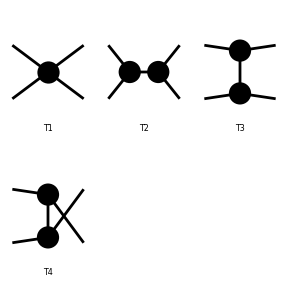

```mathematica
topsLO=CreateTopologies[0, 2->2];
topsR=CreateTopologies[0, 2->3];
(* The SelfEnergy and Tadpoles will not be relevant for the 2to2 *)
topsV=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles}];
topsBox=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles,Triangles,SelfEnergies}];
topsTri=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles,Boxes,SelfEnergies}];
topsSelf=CreateTopologies[1, 2->2,ExcludeTopologies->{Tadpoles,Boxes,Triangles}];
Paint[topsLO];
(*Paint[topsV];*)
(*Paint[topsR];*)
topsCT=CreateCTTopologies[1,2->2];
(*Paint[topsCT]*)
```

```mathematica
ConjugationList={Conjugate[Qu]:>Qu,Conjugate[Qd]:>Qd,Conjugate[Qe]:>Qe};
```

```mathematica
OrganiseSquaredAmpVirt[input_,nweyl_,nqed_]:=Collect[Coefficient[Collect[(2^nweyl)*input//.Abbr[]//.Subexpr[]/.MomReplace/.ConjugationList/.Replacements2to2,{D0i[__],C0i[__],B0i[__],A0[__],Finite},Simplify],Qe,nqed]*Qe^nqed/.Alfas2->ALPHAS^2/.Alfas->ALPHAS/.Alfa2->ALPHA^2/.Den[s12,mz2]->chiz/.Den[s12,Conjugate[mz2]]->Conjugate[chiz]/.Den[a_,b_]:>1/(a-b )/.Den[a_,b_,2]:>1/(a-b)^2/.IGram[a_]:> 1/a/.Diagram[a_]:>1/.Conjugate[s12]->s12,{D0i[__],C0i[__],B0i[__],A0[__],Finite},Simplify];
```

```mathematica
scalarIntegral={Finite->Finite[eps],B0i[bb0,s12,msqQ,msqQ]->B0sQQ[eps],B0i[bb0,s12,0,0]->B0s00[eps],A0[msqQ]->A0Q[eps] ,B0i[bb0,msqQ,0,msqQ]->B0Q0Q[eps],B0i[bb0,0,0,0]->0,B0i[bb0,th,0,msqQ]->B0t0Q[eps],B0i[bb0,uh,0,msqQ]->B0u0Q[eps],C0i[cc0,0,msqQ,th,0,0,msqQ]->C00Qt00Q[eps],C0i[cc0,0,msqQ,uh,0,0,msqQ]->C00Qu00Q[eps],C0i[cc0,0,s12,0,0,0,0]->C0s[eps],C0i[cc0,s12,msqQ,msqQ,0,0,msqQ]->C0sQQ00Q[eps],C0i[cc0,msqQ,s12,msqQ,0,msqQ,msqQ]->C0QsQ0QQ[eps],D0i[dd0,0,s12,msqQ,th,0,msqQ,0,0,0,msqQ]->D00sQt0Q000Q[eps],D0i[dd0,0,s12,msqQ,uh,0,msqQ,0,0,0,msqQ]->D00SQu0Q000Q[eps],C0i[cc0,0,s12,0,msqQ,msqQ,msqQ]->C00s0QQQ[eps],
C0i[cc0,0,th,msqQ,0,0,msqQ]->C00tQ00Q[eps],
C0i[cc0,0,uh,msqQ,0,0,msqQ]->C00uQ00Q[eps],
C0i[cc0,msqQ,0,th,0,msqQ,msqQ]->C0Q0t0QQ[eps],
C0i[cc0,msqQ,0,uh,0,msqQ,msqQ]->C0Q0u0QQ[eps]}
```

{Finite→Finite(eps),B0i(bb0,s12,msqQ,msqQ)→B0sQQ(eps),B0i(bb0,s12,0,0)→B0s00(eps),A0(msqQ)→A0Q(eps),B0i(bb0,msqQ,0,msqQ)→B0Q0Q(eps),B0i(bb0,0,0,0)→0,B0i(bb0,th,0,msqQ)→B0t0Q(eps),B0i(bb0,uh,0,msqQ)→B0u0Q(eps),C0i(cc0,0,msqQ,th,0,0,msqQ)→C00Qt00Q(eps),C0i(cc0,0,msqQ,uh,0,0,msqQ)→C00Qu00Q(eps),C0i(cc0,0,s12,0,0,0,0)→C0s(eps),C0i(cc0,s12,msqQ,msqQ,0,0,msqQ)→C0sQQ00Q(eps),C0i(cc0,msqQ,s12,msqQ,0,msqQ,msqQ)→C0QsQ0QQ(eps),D0i(dd0,0,s12,msqQ,th,0,msqQ,0,0,0,msqQ)→D00sQt0Q000Q(eps),D0i(dd0,0,s12,msqQ,uh,0,msqQ,0,0,0,msqQ)→D00SQu0Q000Q(eps),C0i(cc0,0,s12,0,msqQ,msqQ,msqQ)→C00s0QQQ(eps),C0i(cc0,0,th,msqQ,0,0,msqQ)→C00tQ00Q(eps),C0i(cc0,0,uh,msqQ,0,0,msqQ)→C00uQ00Q(eps),C0i(cc0,msqQ,0,th,0,msqQ,msqQ)→C0Q0t0QQ(eps),C0i(cc0,msqQ,0,uh,0,msqQ,msqQ)→C0Q0u0QQ(eps)}

```mathematica
(* Useful for shortening some expressions, keeping more invariants *)
```

```mathematica
(* Now simplify the R in powers of the electron Qed coupling *)
```

```mathematica
OrganiseSquaredAmpR[input_,nweyl_,nqed_]:=
Simplify[
Collect[
Collect[
Coefficient[(2^nweyl)*input//.Abbr[]//.SubExpr[]/.MomReplace/.ConjugationList,Qe,nqed]*Qe^nqed/.Den[s12,mz2]->chiz/.Den[s12,Conjugate[mz2]]->Conjugate[chiz]/.Den[a_,b_]:>1/(a- b )/.Replacements2to3,Eps[__],Simplify][[1]]/.PassarinoId/.EpsEtaReplace/.EpsRotReplace/.Replacements2to3,Pair[__],Simplify][[1]]/.InverseReplacements2to3]
```

```mathematica
(* For quark computation *)
```

```mathematica
MD=MD2=0;
MU=MU2=0;
```

## 1. neutrino photon interactions: nu + gamma > X

### 1.1) Squared Amplitude calculation, CC quark line: nu + lepton > quarks (3,4) + photon(5), valid beyond resonant propagator when Γ -> 0

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 4 Particles insertions

> Top. 12: 2 Particles insertions

> Top. 13: 2 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 2 Particles insertions

in total: 10 Particles insertions

> Top. 1 afbf/cgdgeh/fhgh.m, 0 diagrams

> Top. 2 afbf/cgdheg/fhgh.m, 0 diagrams

> Top. 3 afbf/cgdheh/fggh.m, 0 diagrams

> Top. 4 afbg/chdheg/fgfh.m, 0 diagrams

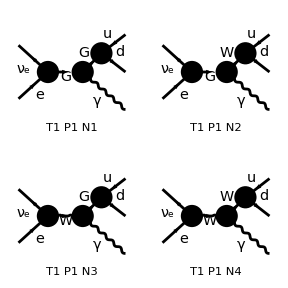

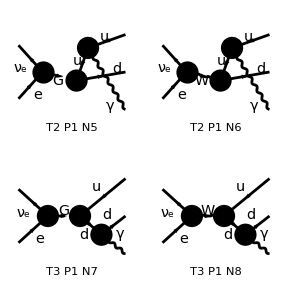

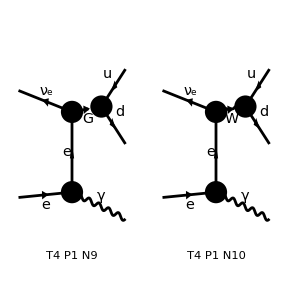

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],F[2,{1}]}->{-F[3,{1}],F[4,{1}],V[1]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 10 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->4]/.MW2->mw2/.SW2->sw2;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 144 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3/.ConjugationList/.EpsRotReplace/.EpsEtaReplace/.PassarinoId/.Replacements2to3/.m4sq->0/.m5sq->0/.m3sq->0/.ME2->0/.Den[a_,b_]:>1/(a - b ),{Eps[__]},Simplify][[1]]/.Qd->Qe/3/.Qu->-Qe*2/3/.Qe->-1/.Pair[eta[5],k[2]]->Pair[eta[5],k[3]]+Pair[eta[5],k[4]]+Pair[eta[5],k[5]]-Pair[eta[5],k[1]],{Pair[__]},Simplify][[1]]
```

(4 Alfa Alfa2 π^3 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) (2 s12 (s12-s15-s25) ((3 s13+s15-3 s24-2 s25) (3 s24+2 s25)+s12 (-6 s13+6 s24+4 s25))+mw2 (4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2)))+(4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+2 mw2 (9 s13^2+s13 (9 s15-9 s24-6 s25)-6 s15 (s24+s25)+s12 (-6 s13+6 s24+4 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2))) mw2^*))/(3 (mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*)+(Alfa Alfa2 π^3 (s15+s25) (12 s13^2+s15^2-7 s15 s24+12 s24^2+s13 (7 s15-24 s24-11 s25)-3 s15 s25+11 s24 s25+2 s25^2) (mw2-mw2^*) ((s13-s24-s25) Eps[eta[5],k[1],k[2],k[3]]+(s13+s15-s24) Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]]) Pair[eta[5],k[1]])/((mw2-s12) (s13+s15-s24) s25 (mw2-s12+s15+s25) (-s13+s24+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^* Pair[eta[5],k[5]]^2)+1/Pair[eta[5],k[5]]^2((Alfa Alfa2 π^3 (-3 s15^3+12 s13^2 (s15+s25)+s15^2 (5 s24+7 s25)+s15 (12 s24^2+s24 s25-6 s25^2)+4 s25 (3 s24^2+5 s24 s25+2 s25^2)-s13 (5 s15^2+s15 (24 s24+s25)+4 s25 (6 s24+5 s25))) (mw2-mw2^*) ((s13-s24-s25) Eps[eta[5],k[1],k[2],k[3]]+(s13+s15-s24) Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]]) Pair[eta[5],k[3]])/((mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*)+(Alfa Alfa2 π^3 (4 s13+s15-4 s24) (3 s13+s15-3 s24-2 s25) (s15+s25) (mw2-mw2^*) ((s13-s24-s25) Eps[eta[5],k[1],k[2],k[3]]+(s13+s15-s24) Eps[eta[5],k[1],k[2],k[4]]-s25 Eps[eta[5],k[1],k[3],k[4]]+s15 Eps[eta[5],k[2],k[3],k[4]]) Pair[eta[5],k[4]])/((mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*))+(Alfa Alfa2 π^3 (3 s13+s15-3 s24-2 s25) (mw2-mw2^*) ((-8 s13^3+s13^2 (-12 s15+8 s24+12 s25)+s13 (-7 s15^2+8 s24^2+12 s24 s25+3 s25^2+12 s15 (s24+s25))+2 (2 s15^3+s15 s25 (2 s24+s25)+s15^2 (4 s24+5 s25)-2 (2 s24^3+6 s24^2 s25+5 s24 s25^2+s25^3))+s12 (16 s13^2-4 s15^2-16 s15 s24+16 s24^2-15 s15 s25+32 s24 s25+13 s25^2+16 s13 (s15-2 (s24+s25)))) Eps[eta[5],k[1],k[2],k[3]]+(-8 s13^3-7 s15^3+4 s15^2 s24+8 s15 s24^2-8 s24^3+2 s15^2 s25+8 s15 s24 s25-16 s24^2 s25+9 s15 s25^2-12 s24 s25^2+4 s13^2 (-5 s15+2 s24+s25)+s12 (16 s13^2+15 s15^2-28 s15 s24+16 s24^2+4 s13 (7 s15-8 s24-5 s25)-17 s15 s25+20 s24 s25)+s13 (-19 s15^2+12 s15 s24+8 s24^2+8 s15 s25+12 s24 s25+11 s25^2)) Eps[eta[5],k[1],k[2],k[4]]-4 s12 s15^2 Eps[eta[5],k[1],k[3],k[4]]+4 s15^2 s24 Eps[eta[5],k[1],k[3],k[4]]-16 s12 s13 s25 Eps[eta[5],k[1],k[3],k[4]]+8 s13^2 s25 Eps[eta[5],k[1],k[3],k[4]]-15 s12 s15 s25 Eps[eta[5],k[1],k[3],k[4]]+12 s13 s15 s25 Eps[eta[5],k[1],k[3],k[4]]+11 s15^2 s25 Eps[eta[5],k[1],k[3],k[4]]+16 s12 s24 s25 Eps[eta[5],k[1],k[3],k[4]]+4 s15 s24 s25 Eps[eta[5],k[1],k[3],k[4]]-8 s24^2 s25 Eps[eta[5],k[1],k[3],k[4]]+13 s12 s25^2 Eps[eta[5],k[1],k[3],k[4]]-4 s13 s25^2 Eps[eta[5],k[1],k[3],k[4]]-s15 s25^2 Eps[eta[5],k[1],k[3],k[4]]-8 s24 s25^2 Eps[eta[5],k[1],k[3],k[4]]-4 s25^3 Eps[eta[5],k[1],k[3],k[4]]+12 s12 s13 s15 Eps[eta[5],k[2],k[3],k[4]]-8 s13^2 s15 Eps[eta[5],k[2],k[3],k[4]]+15 s12 s15^2 Eps[eta[5],k[2],k[3],k[4]]-8 s13 s15^2 Eps[eta[5],k[2],k[3],k[4]]-7 s15^3 Eps[eta[5],k[2],k[3],k[4]]-12 s12 s15 s24 Eps[eta[5],k[2],k[3],k[4]]-4 s15^2 s24 Eps[eta[5],k[2],k[3],k[4]]+8 s15 s24^2 Eps[eta[5],k[2],k[3],k[4]]-4 s12 s13 s25 Eps[eta[5],k[2],k[3],k[4]]-17 s12 s15 s25 Eps[eta[5],k[2],k[3],k[4]]+4 s13 s15 s25 Eps[eta[5],k[2],k[3],k[4]]+s15^2 s25 Eps[eta[5],k[2],k[3],k[4]]+4 s12 s24 s25 Eps[eta[5],k[2],k[3],k[4]]+12 s15 s24 s25 Eps[eta[5],k[2],k[3],k[4]]+4 s13 s25^2 Eps[eta[5],k[2],k[3],k[4]]+8 s15 s25^2 Eps[eta[5],k[2],k[3],k[4]]))/((mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^* Pair[eta[5],k[5]])

```mathematica
result/.Eps[__]->0
```

(4 Alfa Alfa2 π^3 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) (2 s12 (s12-s15-s25) ((3 s13+s15-3 s24-2 s25) (3 s24+2 s25)+s12 (-6 s13+6 s24+4 s25))+mw2 (4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2)))+(4 s12^2 (3 s13-3 s24-2 s25)+s12 (-9 s13^2+9 s15 s24+9 s24^2+8 s15 s25+18 s24 s25+8 s25^2-3 s13 (5 s15+2 s25))+2 mw2 (9 s13^2+s13 (9 s15-9 s24-6 s25)-6 s15 (s24+s25)+s12 (-6 s13+6 s24+4 s25))+3 (3 s13^2 s25+s15 (s15-3 s24-2 s25) (s24+s25)+s13 (3 s15 s24+4 s15 s25-3 s24 s25-2 s25^2))) mw2^*))/(3 (mw2-s12) (s13+s15-s24) (s13-s24-s25) s25 (mw2-s12+s15+s25) sw2 (s12-mw2^*) (-s12+s15+s25+mw2^*) sw2^*)

```mathematica
(* Try to combine / find some common factors for simplifications *)
```

```mathematica
prefac=1/(s35^2 s45^2)2048 Alfa2 Alfas π^3;
```

```mathematica
RresTemp[1]
```

-1/(s12 s35^2 s45^2)2048 Alfa2 Alfas π^3 Qe Qu (chiz (gLe gLu (2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45)+gRe gRu (2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45)+gLu gRe (2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45))+gLe gRu (2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)))+chiz^* (gRe^* ((2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)) gLu^*+(2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45) gRu^*)+gLe^* ((2 MT2^2 s12 (s15+s25)^2+2 MT2 (s12^2 (s13^2+s15^2+s24^2+s13 (s15-2 s24-s25)+s24 s25+s25^2+s15 (-s24+s25))+(s13 s25+s15 (s24+s25))^2-s12 (s15+s25) (s13^2+s13 (s15-2 s24+s25)+(s15+s24) (s24+s25)))-s12 (2 s12^2+s13^2+2 s13 s15+s15^2+s24^2+2 s24 s25+s25^2-2 s12 (s13+s15+s24+s25)) s35 s45) gLu^*+(2 MT2^2 s12 (s15+s25)^2-s12 (s13^2+s24^2) s35 s45+2 MT2 ((s13 s25+s15 (s24+s25))^2-s12^2 s35 s45+s12 (s15+s25) s35 s45)) gRu^*)))

```mathematica
CForm[prefac/.Alfa2->ALPHA^2]/.Pi->pi/.Power->pow/.Alfas->ALPHAS
```

2048*ALPHAS*pow(ALPHA,2)*pow(pi,3)*pow(s35,-2)*pow(s45,-2)

```mathematica
CForm[Rexpr]/.MT2->msqQ/.Qu->Q2/.Qe->Q1/.gLe->gLf1/.gRe->gRf1/.gLu->gLf2/.gRu->gRf2/.Power->pow/.Conjugate->conj/.chiz->chizs
```

-(chizs*conj(chizs)*(gLf1*conj(gLf1)*(conj(gRf2)*
            (-2*gLf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gRf2*(-(s12*s35*s45*(pow(s13,2) + pow(s24,2))) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))))) + 
           conj(gLf2)*(-2*gRf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gLf2*(-2*s35*s45*pow(s12,3) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))) - 
                 2*pow(s12,2)*(-((s15 - s24)*(s24 + s25)*(s15 + s24 + s25)) + 
                    (2*s15 - s24)*pow(s13,2) + pow(s13,3) - msqQ*pow(s15 + s25,2) + 
                    s13*(-(s15*(2*s24 + s25)) + pow(s15,2) - pow(s24 + s25,2))) + 
                 s12*((3*s15 - 2*s24 - s25)*pow(s13,3) + pow(s13,4) + 
                    pow(s13,2)*(-5*s15*s24 + (-3*s15 + 3*s24)*s25 + 3*pow(s15,2) + 2*pow(s24,2) + 
                       pow(s25,2)) + s13*(-((4*s24 + 3*s25)*pow(s15,2)) + pow(s15,3) - 
                       5*s25*pow(s24,2) + s15*(s25*(-4*msqQ + 4*s24 + s25) + 3*pow(s24,2)) - 
                       2*pow(s24,3) + (-4*msqQ - 4*s24 - s25)*pow(s25,2)) - 
                    (s24 + s25)*(4*msqQ*s15*(s15 + s25) + (s15 - s24)*(pow(s15,2) + pow(s24 + s25,2))))
                 ))) + gRf1*conj(gRf1)*(conj(gLf2)*
            (-2*gRf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gLf2*(-(s12*s35*s45*(pow(s13,2) + pow(s24,2))) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))))) + 
           conj(gRf2)*(-2*gLf2*msqQ*(s35*s45*(-(s15*s25) + pow(s12,2)) + 
                 s12*(s15 + s25)*(s13*(s15 - 2*s24 - s25) - msqQ*(s15 + s25) - 
                    (s15 - s24)*(s24 + s25) + pow(s13,2))) + 
              gRf2*(-2*s35*s45*pow(s12,3) + 
                 2*msqQ*(s15 + s25)*(s25*pow(s13,2) + s15*((s13 + s24)*s25 + pow(s24,2))) - 
                 2*pow(s12,2)*(-((s15 - s24)*(s24 + s25)*(s15 + s24 + s25)) + 
                    (2*s15 - s24)*pow(s13,2) + pow(s13,3) - msqQ*pow(s15 + s25,2) + 
                    s13*(-(s15*(2*s24 + s25)) + pow(s15,2) - pow(s24 + s25,2))) + 
                 s12*((3*s15 - 2*s24 - s25)*pow(s13,3) + pow(s13,4) + 
                    pow(s13,2)*(-5*s15*s24 + (-3*s15 + 3*s24)*s25 + 3*pow(s15,2) + 2*pow(s24,2) + 
                       pow(s25,2)) + s13*(-((4*s24 + 3*s25)*pow(s15,2)) + pow(s15,3) - 
                       5*s25*pow(s24,2) + s15*(s25*(-4*msqQ + 4*s24 + s25) + 3*pow(s24,2)) - 
                       2*pow(s24,3) + (-4*msqQ - 4*s24 - s25)*pow(s25,2)) - 
                    (s24 + s25)*(4*msqQ*s15*(s15 + s25) + (s15 - s24)*(pow(s15,2) + pow(s24 + s25,2))))
                 ))))) - 2*pow(Q1,2)*pow(Q2,2)*pow(s12,-2)*
    (-(s12*s35*s45*(-2*s12*(s13 + s15 + s24 + s25) + 2*(s13*s15 + pow(s12,2) + pow(s13,2)) + 
           pow(s15,2) + 2*(s24*s25 + pow(s24,2)) + pow(s25,2))) + 4*s12*pow(msqQ,2)*pow(s15 + s25,2) + 
      2*msqQ*(-2*s12*(s15 + s25)*(s13*(s15 - 2*s24) + s24*(s24 + s25) + pow(s13,2)) + 
         pow(s12,2)*(-2*s15*s24 + 2*pow(s13,2) + pow(s15,2) + 
            2*(s13*(s15 - 2*s24 - s25) + s24*s25 + pow(s24,2)) + pow(s25,2)) + 
         2*pow(s13*s25 + s15*(s24 + s25),2))) - 
   Q1*Q2*pow(s12,-1)*(chizs*((gLf2*gRf1 + gLf1*gRf2)*
          (s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 2*pow(msqQ,2)*pow(s15 + s25,2)) + 
            2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
         (gLf1*gLf2 + gRf1*gRf2)*(-(s12*s35*s45*
               (2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 2*pow(s12,2) + pow(s13,2) + 
                 pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
            2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
               msqQ*(-(s12*(s15 + s25)*(s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + 
                       pow(s13,2))) + pow(s12,2)*
                   (s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + pow(s15,2) + 
                     pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2))))) + 
      conj(chizs)*(conj(gLf1)*(conj(gRf2)*
             (s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 2*pow(msqQ,2)*pow(s15 + s25,2)) + 
               2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
            conj(gLf2)*(-(s12*s35*s45*(2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 
                    2*pow(s12,2) + pow(s13,2) + pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
               2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
                  msqQ*(-(s12*(s15 + s25)*
                        (s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + pow(s13,2))) + 
                     pow(s12,2)*(s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + 
                        pow(s15,2) + pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2))))) + 
         conj(gRf1)*(conj(gLf2)*(s12*(-(s35*s45*(pow(s13,2) + pow(s24,2))) + 
                  2*pow(msqQ,2)*pow(s15 + s25,2)) + 
               2*msqQ*(s35*s45*(s12*(s15 + s25) - pow(s12,2)) + pow(s13*s25 + s15*(s24 + s25),2))) + 
            conj(gRf2)*(-(s12*s35*s45*(2*s13*s15 + 2*s24*s25 - 2*s12*(s13 + s15 + s24 + s25) + 
                    2*pow(s12,2) + pow(s13,2) + pow(s15,2) + pow(s24,2) + pow(s25,2))) + 
               2*(s12*pow(msqQ,2)*pow(s15 + s25,2) + 
                  msqQ*(-(s12*(s15 + s25)*
                        (s13*(s15 - 2*s24 + s25) + (s15 + s24)*(s24 + s25) + pow(s13,2))) + 
                     pow(s12,2)*(s13*(s15 - 2*s24 - s25) - s15*(s24 - s25) + s24*s25 + pow(s13,2) + 
                        pow(s15,2) + pow(s24,2) + pow(s25,2)) + pow(s13*s25 + s15*(s24 + s25),2)))))))

```mathematica
(* One could also introduce sub-expressions to speed up computation *)
```

```mathematica
Clear[SubExpr]
```

```mathematica
test=Abbreviate[Rexpr,6]
```

-1/s12^2 2 Qe^2 Qu^2 (4 MT2^2 s12 (s15+s25)^2-s12 (s15^2+2 (s12^2+s13^2+s13 s15)+s25^2-2 s12 (s13+s15+s24+s25)+2 (s24^2+s24 s25)) s35 s45+2 MT2 (2 (s13 s25+s15 (s24+s25))^2-2 s12 (s15+s25) Sub1+s12^2 Sub3))-1/s12 Qe Qu (chiz ((gLe gLu+gRe gRu) (2 Sub19-s12 s35 s45 Sub20)+(gLu gRe+gLe gRu) (s12 Sub21+2 MT2 Sub22))+chiz^* (Sub24 gLe^*+Sub23 gRe^*))-chiz chiz^* (gRe gRe^* ((gLu Sub5-2 gRu MT2 Sub7) gLu^*+(gRu Sub15-2 gLu MT2 Sub7) gRu^*)+gLe gLe^* ((gLu Sub15-2 gRu MT2 Sub7) gLu^*+(gRu Sub5-2 gLu MT2 Sub7) gRu^*))

### 1.2) Squared Amplitude calculation, NC lepton line: nu + gamma > nu (3) + quark (4,5) [Complete]

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 1 Particles insertion

> Top. 15: 1 Particles insertion

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheg/fhgh.m, 0 diagrams

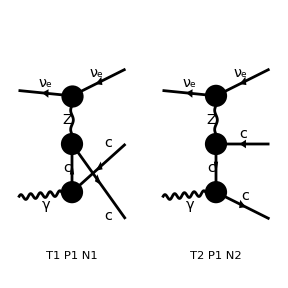

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],V[1]}->{-F[1,{1}],-F[3,{2}],F[3,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->5]/.MZ2->mz2/.MW2->mw2/.SW2->sw2;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 64 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
Replacements2to3/.m[3]^2->0/.m[4]^2->MC2/.m[5]^2->MC2/.m[2]^2->0/.m[1]^2->0
```

{s14→s12-s13-s15,s23→s12-s24-s25,s34→s12-s15-s25,s35→s13+s15-s24,s45→-2 MC2-s13+s24+s25}

```mathematica
(* Eps[eta[2],k[1],k[4],k[5]] *)
```

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3/.m[3]^2->0/.m[4]^2->MC2/.m[5]^2->MC2/.m[2]^2->0/.m[1]^2->0,{Eps[__]},Simplify]/.Den[a_,b_]:>1/(a - b ),{Pair[__]},Simplify]
```

1/((mz2+s13) s24^2 s25^2 (s13+mz2^*))96 Alfa Alfa2 gLnu π^3 Qu^2 gLnu^* ((-2 gRu MC2^2 s13 (s24+s25)^2+gLu s13 s24 s25 (s12^2+2 s15^2+2 s15 s25+s25^2-2 s12 (s15+s25))+2 gLu MC2 (s24+s25) (s12^2 s24-s12 s24 (2 s15+s25)+s15^2 (s24+s25))+2 gRu MC2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gLu^*+(gRu s13 s24 (s12^2+2 s13^2+4 s13 s15+2 s15^2-2 s12 (s13+s15)-2 s13 s24-2 s15 s24+s24^2) s25-2 gLu MC2^2 s13 (s24+s25)^2+2 gRu MC2 (s24+s25) (s12^2 s24-s12 s24 (2 s13+2 s15+s25)+(s13+s15)^2 (s24+s25))+2 gLu MC2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gRu^*)

```mathematica
(* Result for implementation in c++ code, the quark result related by nc and Qe gLe gRe replacement *)
```

```mathematica
(* Additional factor for weyl fermions and photon averaging = 2^4 / 2*)
```

```mathematica
2^4/2
```

8

```mathematica
prefac=1/(s24^2 s25^2)32 Alfa Alfa2 π^3 chiz13 Conjugate[chiz13]gLnu Conjugate[gLnu]Qu^2;
```

```mathematica
CForm[prefac/.Qu->Qf]/.Conjugate->conj/.Pi->pi/.Alfa2->ALPHA^2/.Alfa->ALPHA/.Power->pow
```

32*chiz13*gLnu*conj(chiz13)*conj(gLnu)*pow(ALPHA,3)*pow(pi,3)*pow(Qf,2)*pow(s24,-2)*pow(s25,-2)

```mathematica
CForm[(result/.(mz2+s13)->1/chiz13/.(Conjugate[mz2]+s13)->1/Conjugate[chiz13])/prefac/.MM2->mfsq/.Conjugate->conj/.Power->pow]/.MC2->mfsq/.gRu->gRf/.gLu->gLf
```

3*(conj(gRf)*(2*gLf*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - pow(s12,2)) + 
        2*gRf*mfsq*(s24 + s25)*(-(s12*s24*(2*s13 + 2*s15 + s25)) + s24*pow(s12,2) + 
           (s24 + s25)*pow(s13 + s15,2)) + 
        gRf*s13*s24*s25*(4*s13*s15 - 2*s12*(s13 + s15) - 2*s13*s24 - 2*s15*s24 + pow(s12,2) + 
           2*pow(s13,2) + 2*pow(s15,2) + pow(s24,2)) - 2*gLf*s13*pow(mfsq,2)*pow(s24 + s25,2)) + 
     conj(gLf)*(2*gRf*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - pow(s12,2)) + 
        2*gLf*mfsq*(s24 + s25)*(-(s12*s24*(2*s15 + s25)) + s24*pow(s12,2) + (s24 + s25)*pow(s15,2)) + 
        gLf*s13*s24*s25*(2*s15*s25 - 2*s12*(s15 + s25) + pow(s12,2) + 2*pow(s15,2) + pow(s25,2)) - 
        2*gRf*s13*pow(mfsq,2)*pow(s24 + s25,2)))

### 1.3) Squared Amplitude calculation, NC lepton line: nu + gamma > nu (3) + lepton (4,5) [Complete]

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 1 Particles insertion

> Top. 15: 1 Particles insertion

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 2 afbg/cfdheg/fhgh.m, 0 diagrams

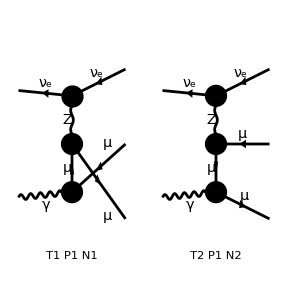

```mathematica
insertFieldseeQQbR=InsertFields[topsR,{-F[1,{1}],V[1]}->{-F[1,{1}],-F[2,{2}],F[2,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldseeQQbR,ColumnsXRows->{2,2}];
```

```mathematica
feynampR=CreateFeynAmp[insertFieldseeQQbR];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeR=CalcFeynAmp[feynampR,FermionChains->Chiral,Invariants->False,MomElim->5]/.MW2->mw2/.MZ2->mz2/.SW2->sw2;
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpQQbR=PolarizationSum[AmplitudeR,GaugeTerms->True];
```

> 64 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
(* Eps[eta[2],k[1],k[4],k[5]] *)
```

```mathematica
result=Collect[
Collect[squaredAmpQQbR//.Abbr[]//.Subexpr[]/.MomReplace/.Replacements2to3/.ConjugationList/.EpsRotate/.EpsReplace/.PassarinoId2/.EpsRotate/.EpsReplace/.Replacements2to3/.m4sq->MM2/.m5sq->MM2/.m3sq->0,{Eps[__]},Simplify][[1]]/.Den[a_,b_]:>1/(a - b ),{Pair[__]},Simplify][[1]]
```

(32 Alfa Alfa2 gLnu π^3 Qe^2 gLnu^* ((-2 gRe MM2^2 s13 (s24+s25)^2+gLe s13 s24 s25 (s12^2+2 s15^2+2 s15 s25+s25^2-2 s12 (s15+s25))+2 gLe MM2 (s24+s25) (s12^2 s24-s12 s24 (2 s15+s25)+s15^2 (s24+s25))+2 gRe MM2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gLe^*+(gRe s13 s24 (s12^2+2 s13^2+4 s13 s15+2 s15^2-2 s12 (s13+s15)-2 s13 s24-2 s15 s24+s24^2) s25-2 gLe MM2^2 s13 (s24+s25)^2+2 gRe MM2 (s24+s25) (s12^2 s24-s12 s24 (2 s13+2 s15+s25)+(s13+s15)^2 (s24+s25))+2 gLe MM2 s24 s25 (-s12^2+s12 (s24+s25)+s13 (-s13+s24+s25))) gRe^*))/((mz2+s13) s24^2 s25^2 (s13+mz2^*))

```mathematica
(* Result for implementation in c++ code, the quark result related by nc and Qe gLe gRe replacement *)
```

```mathematica
prefac=1/(s24^2 s25^2)32 Alfa Alfa2 π^3 chiz13 Conjugate[chiz13]gLnu Conjugate[gLnu]Qe^2;
```

```mathematica
CForm[(result/.(mz2+s13)->1/chiz13/.(Conjugate[mz2]+s13)->1/Conjugate[chiz13])/prefac/.MM2->mfsq/.Conjugate->conj/.Power->pow]
```

conj(gRe)*(2*gLe*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - pow(s12,2)) + 
      2*gRe*mfsq*(s24 + s25)*(-(s12*s24*(2*s13 + 2*s15 + s25)) + s24*pow(s12,2) + 
         (s24 + s25)*pow(s13 + s15,2)) + 
      gRe*s13*s24*s25*(4*s13*s15 - 2*s12*(s13 + s15) - 2*s13*s24 - 2*s15*s24 + 
         pow(s12,2) + 2*pow(s13,2) + 2*pow(s15,2) + pow(s24,2)) - 
      2*gLe*s13*pow(mfsq,2)*pow(s24 + s25,2)) + 
   conj(gLe)*(2*gRe*mfsq*s24*s25*(s12*(s24 + s25) + s13*(-s13 + s24 + s25) - 
         pow(s12,2)) + 2*gLe*mfsq*(s24 + s25)*
       (-(s12*s24*(2*s15 + s25)) + s24*pow(s12,2) + (s24 + s25)*pow(s15,2)) + 
      gLe*s13*s24*s25*(2*s15*s25 - 2*s12*(s15 + s25) + pow(s12,2) + 2*pow(s15,2) + 
         pow(s25,2)) - 2*gRe*s13*pow(mfsq,2)*pow(s24 + s25,2))

## 2. neutrino-neutrino interactions:

### 2.1) LO Squared Amplitude calculation nu nubar > ffbar

loading generic model file /Users/rhorry/Research/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SMQCD.mod

loading classes model file /Users/rhorry/Research/FeynArts-3.11/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

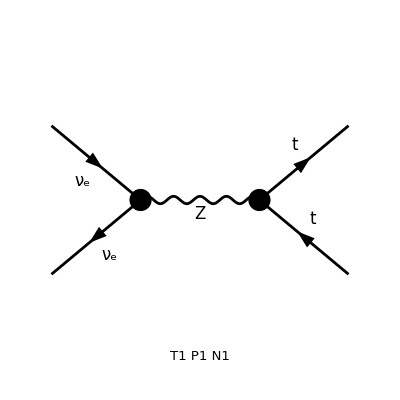

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{F[3,{3}],-F[3,{3}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp((F(1,{1}) | k(1) | 0 | {0,LeptonNumber}
-F(1,{1}) | k(2) | 0 | {0,-LeptonNumber})→(F(3,{3,Col3}) | k(3) | MT | {(2 Charge)/3,(2 ColorCharge)/(√3)}
-F(3,{3,Col4}) | k(4) | MT | {-(2 Charge)/3,-(2 ColorCharge)/(√3)}))(-4 π Alfa gLnu gRu Mat(F1 SUN1) Den(2 Pair(k(1),k(2)),mz2)-4 π Alfa gLnu gLu Mat(F2 SUN1) Den(2 Pair(k(1),k(2)),mz2))

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 4 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp*chiz*Conjugate[chiz]*(s12-mz2)*(s12-Conjugate[mz2])//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

192 π^2 Alfa2 chiz gLnu Conjugate[chiz] Conjugate[gLnu] (Conjugate[gRf] (gLf mfsq s12+gRf s13^2)+Conjugate[gLf] (gLf (s12-s13)^2+gRf mfsq s12))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

192*Alfa2*chiz*gLnu*conj(chiz)*conj(gLnu)*pow(Pi,2)*
   (conj(gLf)*(gRf*mfsq*s12 + gLf*pow(s12 - s13,2)) + conj(gRf)*(gLf*mfsq*s12 + gRf*pow(s13,2)))

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.2) LO Squared Amplitude calculation nu1 nu1 > nu1 nu1

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

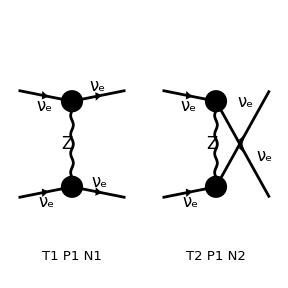

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{F[1,{1}],k[2],0,{0,LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{F[1,{1}],k[4],0,{0,LeptonNumber}}}][8 Alfa gLnu^2 π (Den[-2 Pair[k[1],k[3]],mz2]+Den[-2 Pair[k[1],k[4]],mz2]) Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 s12^2 (2 mz2+s12) (gLnu^*)^2 (s12+2 mz2^*))/((mz2+s12-s13) (mz2+s13) (s12-s13+mz2^*) (s13+mz2^*))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.Pi->pi
```

64*ALPHA*(2*MZ2C + s12)*conj(ALPHA)*(s12 + 2*conj(MZ2C))*pow(gLnu,2)*pow(pi,2)*pow(s12,2)*
   pow(MZ2C + s12 - s13,-1)*pow(MZ2C + s13,-1)*pow(conj(gLnu),2)*pow(s12 - s13 + conj(MZ2C),-1)*
   pow(s13 + conj(MZ2C),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.3) LO Squared Amplitude calculation nu1 nu2 > nu1 nu2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

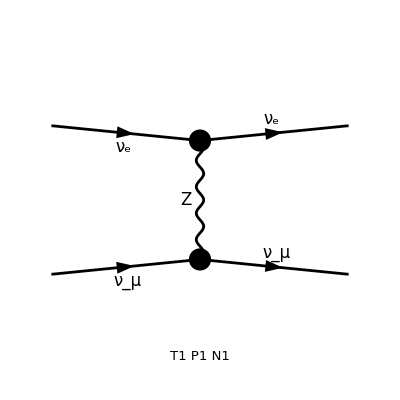

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],F[1,{2}]}->{F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp((F(1,{1}) | k(1) | 0 | {0,LeptonNumber}
F(1,{2}) | k(2) | 0 | {0,LeptonNumber})→(F(1,{1}) | k(3) | 0 | {0,LeptonNumber}
F(1,{2}) | k(4) | 0 | {0,LeptonNumber}))(8 π Alfa gLnu^2 Mat(F1) Den(-2 Pair(k(1),k(3)),mz2))

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 π^2 Alfa2 gLnu^2 s12^2 (Conjugate[gLnu])^2)/((mz2+s13) (Conjugate[mz2]+s13))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.Pi->pi
```

64*ALPHA*conj(ALPHA)*pow(gLnu,2)*pow(pi,2)*pow(s12,2)*pow(MZ2C + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(MZ2C),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.4) LO Squared Amplitude calculation nu1 nu2bar > nu1 nu2bar

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

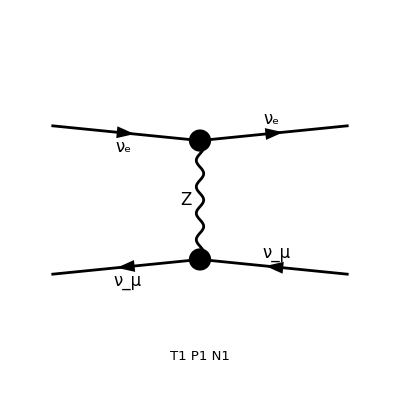

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{2}]}->{F[1,{1}],-F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{2}],k[2],0,{0,-LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{-F[1,{2}],k[4],0,{0,-LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.5) LO Squared Amplitude calculation nu1bar nu2 > nu1bar nu2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

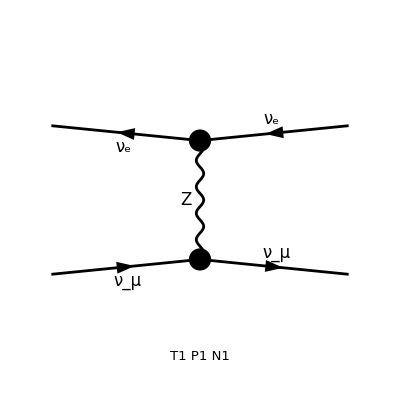

```mathematica
insertFields=InsertFields[topsLO,{-F[1,{1}],F[1,{2}]}->{-F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{-F[1,{1}],k[1],0,{0,-LeptonNumber}},{F[1,{2}],k[2],0,{0,LeptonNumber}}}→{{-F[1,{1}],k[3],0,{0,-LeptonNumber}},{F[1,{2}],k[4],0,{0,LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.6) LO Squared Amplitude calculation nu1 nu1bar > nu1 nu1bar

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

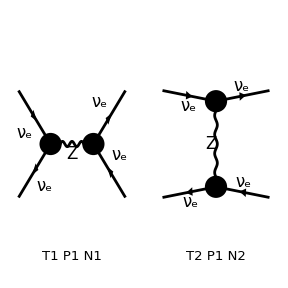

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{F[1,{1}],-F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{1}],k[2],0,{0,-LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{-F[1,{1}],k[4],0,{0,-LeptonNumber}}}][-4 Alfa gLnu^2 π (Den[2 Pair[k[1],k[2]],mz2]+Den[-2 Pair[k[1],k[3]],mz2]) Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (2 mz2-s12+s13) (gLnu^*)^2 (s12-s13-2 mz2^*))/((mz2-s12) (mz2+s13) (s12-mz2^*) (s13+mz2^*))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.Pi->pi
```

64*ALPHA*(2*MZ2C - s12 + s13)*conj(ALPHA)*(s12 - s13 - 2*conj(MZ2C))*pow(gLnu,2)*pow(pi,2)*
   pow(MZ2C - s12,-1)*pow(s12 - s13,2)*pow(MZ2C + s13,-1)*pow(conj(gLnu),2)*pow(s12 - conj(MZ2C),-1)*
   pow(s13 + conj(MZ2C),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.7) LO Squared Amplitude calculation nu1 nu1bar > l1 l1bar

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 2 Particles insertions

> Top. 4: 0 Particles insertions

in total: 3 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

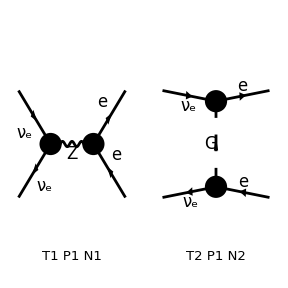

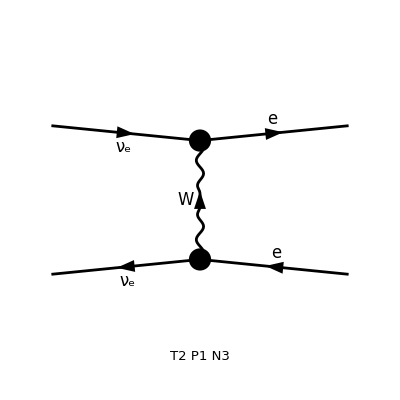

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{F[2,{1}],-F[2,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

in total: 3 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2/.MW2->mw2/.SW2->sw2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp((F(1,{1}) | k(1) | 0 | {0,LeptonNumber}
-F(1,{1}) | k(2) | 0 | {0,-LeptonNumber})→(F(2,{1}) | k(3) | ME | {-Charge,LeptonNumber}
-F(2,{1}) | k(4) | ME | {Charge,-LeptonNumber}))(π (-Alfa) Mat(F1) (4 gLe gLnu Den(2 Pair(k(1),k(2)),mz2)+(2 Den(ME2-2 Pair(k(1),k(3)),mw2))/sw2)-π Alfa Mat(F2) (4 gLnu gRe Den(2 Pair(k(1),k(2)),mz2)+(ME2 Den(ME2-2 Pair(k(1),k(3)),mw2))/(mw2 sw2)))

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 4 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.ME2->mfsq]/.gRe->gRf/.gLe->gLf
```

-((8 π^2 Alfa2 ((4 Conjugate[gLnu] Conjugate[gRf] Conjugate[mw2] Conjugate[sw2] (-Conjugate[mw2]+mfsq-s13)-mfsq Conjugate[mz2]+mfsq s12) (mfsq mw2 s12 (2 gLf gLnu sw2 (-mfsq+mw2+s13)+mz2-s12)+1/2 s13^2 (mfsq (-4 gLnu gRf mw2 sw2+mz2-s12)+4 gLnu gRf mw2 sw2 (mw2+s13)))+Conjugate[mw2] (2 Conjugate[gLf] Conjugate[gLnu] Conjugate[sw2] (-Conjugate[mw2]+mfsq-s13)-Conjugate[mz2]+s12) (2 mw2 (s12-s13)^2 (2 gLf gLnu sw2 (-mfsq+mw2+s13)+mz2-s12)+mfsq s12 (4 gLnu gRf mw2 sw2 (-mfsq+mw2+s13)+mfsq (mz2-s12)))))/(mw2 sw2 Conjugate[mw2] Conjugate[sw2] (mz2-s12) (s12-Conjugate[mz2]) (-mfsq+mw2+s13) (-Conjugate[mw2]+mfsq-s13)))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.mw2->MW2C/.Pi->pi/.sw2->SW2
```

-8*ALPHA*conj(ALPHA)*pow(MW2C,-1)*pow(pi,2)*pow(MZ2C - s12,-1)*
   (conj(MW2C)*(s12 - conj(MZ2C) + 2*conj(gLf)*conj(gLnu)*(mfsq - s13 - conj(MW2C))*conj(SW2))*
      (mfsq*s12*(mfsq*(MZ2C - s12) + 4*gLnu*gRf*MW2C*(-mfsq + MW2C + s13)*SW2) + 
        2*MW2C*(MZ2C - s12 + 2*gLf*gLnu*(-mfsq + MW2C + s13)*SW2)*pow(s12 - s13,2)) + 
     (mfsq*s12 - mfsq*conj(MZ2C) + 4*conj(gLnu)*conj(gRf)*(mfsq - s13 - conj(MW2C))*conj(MW2C)*
         conj(SW2))*(mfsq*MW2C*s12*(MZ2C - s12 + 2*gLf*gLnu*(-mfsq + MW2C + s13)*SW2) + 
        ((4*gLnu*gRf*MW2C*(MW2C + s13)*SW2 + mfsq*(MZ2C - s12 - 4*gLnu*gRf*MW2C*SW2))*pow(s13,2))/2.))*
   pow(-mfsq + MW2C + s13,-1)*pow(SW2,-1)*pow(mfsq - s13 - conj(MW2C),-1)*pow(conj(MW2C),-1)*
   pow(s12 - conj(MZ2C),-1)*pow(conj(SW2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.8) LO Squared Amplitude calculation nu1 nu2bar > l1 l2bar

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 0 Particles insertions

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

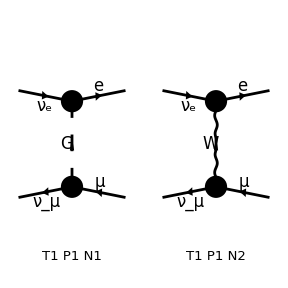

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{2}]}->{F[2,{1}],-F[2,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2/.MW2->mw2/.SW2->sw2
```

preparing FORM code in /Users/rhorry/fc-amp-1.frm

running FORM...

ok

Amp((F(1,{1}) | k(1) | 0 | {0,LeptonNumber}
-F(1,{2}) | k(2) | 0 | {0,-LeptonNumber})→(F(2,{1}) | k(3) | ME | {-Charge,LeptonNumber}
-F(2,{2}) | k(4) | MM | {Charge,-LeptonNumber}))(-(2 π Alfa Mat(F1) Den(ME2-2 Pair(k(1),k(3)),mw2))/sw2-(π Alfa ME MM Mat(F2) Den(ME2-2 Pair(k(1),k(3)),mw2))/(mw2 sw2))

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 4 helicity matrix elements

preparing FORM code in /Users/rhorry/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->ml1sq/.m4sq->ml2sq/.ME2->ml1sq/.MM2->ml2sq]/.gRe->gRf/.gLe->gLf//Simplify
```

(4 π^2 Alfa2 (-2 ml1sq Conjugate[mw2] (ml2sq s12+2 mw2 (s12-s13))+4 mw2 Conjugate[mw2] (s12-s13) (ml2sq-s12+s13)-2 ml1sq ml2sq mw2 s12+ml1sq ml2sq s13 (ml1sq-ml2sq-s13)))/(mw2 sw2 Conjugate[mw2] Conjugate[sw2] (-ml1sq+mw2+s13) (-Conjugate[mw2]+ml1sq-s13))

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.mw2->MW2C/.Pi->pi/.sw2->SW2
```

4*ALPHA*conj(ALPHA)*(-2*ml1sq*ml2sq*MW2C*s12 + ml1sq*ml2sq*(ml1sq - ml2sq - s13)*s13 - 
     2*ml1sq*(ml2sq*s12 + 2*MW2C*(s12 - s13))*conj(MW2C) + 
     4*MW2C*(s12 - s13)*(ml2sq - s12 + s13)*conj(MW2C))*pow(MW2C,-1)*pow(pi,2)*
   pow(-ml1sq + MW2C + s13,-1)*pow(SW2,-1)*pow(ml1sq - s13 - conj(MW2C),-1)*pow(conj(MW2C),-1)*
   pow(conj(SW2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.9) LO Squared Amplitude calculation nu1 gamma > W l1

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 2 Particles insertions

in total: 3 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

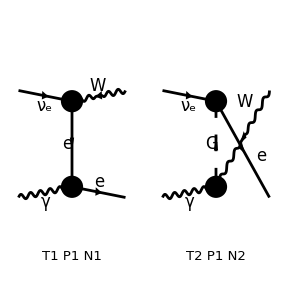

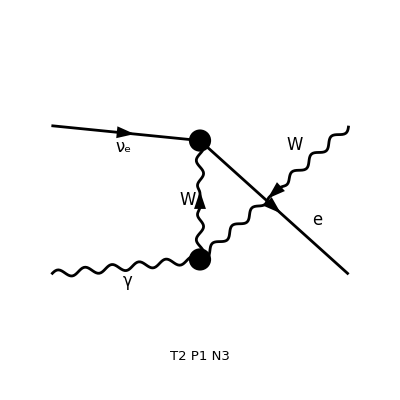

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],V[1]}->{-V[3],F[2,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

in total: 3 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2/.MW2->mw2/.SW2->sw2/.SW->Sqrt[sw2]
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{V[1],k[2],0,{}}}→{{-V[3],k[3],MW,Charge},{F[2,{1}],k[4],ME,{-Charge,LeptonNumber}}}][-(√2 Alfa Pair2 π (2 Qe Den[mw2-2 Pair[k[1],k[3]],ME2]-4 Den[ME2-2 Pair[k[1],k[4]],mw2]) Mat[F1])/(√sw2)-(2 √2 Alfa π Qe Den[mw2-2 Pair[k[1],k[3]],ME2] Mat[F2])/(√sw2)+(√2 Alfa Pair1 π (2 Qe Den[mw2-2 Pair[k[1],k[3]],ME2]-4 Den[ME2-2 Pair[k[1],k[4]],mw2]) Mat[F3])/(√sw2)+(4 √2 Alfa π (Pair3 Qe Den[mw2-2 Pair[k[1],k[3]],ME2]+Pair4 Den[ME2-2 Pair[k[1],k[4]],mw2]) Mat[F4])/(√sw2)]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 16 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^2/2*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mw2r/.m4sq->mlsq/.ME2->mlsq/.Qe->-1]//Simplify
```

(4 Alfa2 π^2 (2 mlsq^4 s12+10 mw2^3 s12^2-6 mw2^2 mw2r s12^2+6 mw2^2 s12^3-10 mw2 mw2r s12^3-12 mw2^3 s12 s13+19 mw2^2 mw2r s12 s13-5 mw2 mw2r^2 s12 s13-17 mw2^2 s12^2 s13+15 mw2 mw2r s12^2 s13-4 mw2r^2 s12^2 s13+8 mw2 s12^3 s13-4 mw2r s12^3 s13+20 mw2^3 s13^2-26 mw2^2 mw2r s13^2+6 mw2 mw2r^2 s13^2+15 mw2^2 s12 s13^2-25 mw2 mw2r s12 s13^2+8 mw2r^2 s12 s13^2-10 mw2 s12^2 s13^2+10 mw2r s12^2 s13^2-18 mw2^2 s13^3+24 mw2 mw2r s13^3-6 mw2r^2 s13^3+12 mw2 s12 s13^3-8 mw2r s12 s13^3-2 mw2 s13^4+2 mw2r s13^4+2 mlsq^3 (2 mw2 s12-2 mw2r s12-2 s12^2-7 mw2 s13+7 mw2r s13+s12 s13)+mlsq^2 (-6 mw2^2 (s12+s13)+mw2 (-4 s12^2-2 mw2r (s12-6 s13)+35 s12 s13-30 s13^2)+2 (mw2r^2 (s12-3 s13)+s12 (s12-s13)^2+mw2r (2 s12^2-17 s12 s13+15 s13^2)))+mlsq (20 mw2^3 s13+mw2^2 (6 mw2r s12-14 s12^2-26 mw2r s13+3 s12 s13-24 s13^2)+2 s13 (mw2r^2 (5 s12-6 s13)+s12 (s12-s13)^2+mw2r (12 s12^2-19 s12 s13+9 s13^2))+mw2 (4 s12^3-2 mw2r^2 (s12-3 s13)-13 s12^2 s13+41 s12 s13^2-18 s13^3+2 mw2r (4 s12^2-9 s12 s13+18 s13^2)))-(2 mlsq^3 s12+20 mw2^3 s13+mlsq^2 (4 mw2 s12-4 mw2r s12-4 s12^2-14 mw2 s13+14 mw2r s13+s12 s13)+2 mw2^2 (3 mw2r s12-3 s12^2-13 mw2r s13+3 s12 s13-9 s13^2)+mw2r s13 (5 mw2r s12+5 s12^2-6 mw2r s13-7 s12 s13+2 s13^2)+mlsq (2 mw2r^2 (s12-3 s13)-6 mw2^2 (s12+s13)+mw2 (-2 s12^2-2 mw2r (s12-6 s13)+21 s12 s13-16 s13^2)+s12 (2 s12^2-s12 s13+s13^2)+4 mw2r (s12^2-5 s12 s13+4 s13^2))+mw2 (-2 mw2r^2 (s12-3 s13)+s13 (-3 s12^2+9 s12 s13-2 s13^2)+mw2r (2 s12^2-13 s12 s13+24 s13^2))) mw2^*) (1/(√sw2))^*)/(mw2 (-mlsq+mw2-s13) (-mlsq+mw2+s12-s13) √sw2 (mlsq+s13-mw2^*) (mlsq-s12+s13-mw2^*))

```mathematica
(* take real part of mw? *)
```

```mathematica
ansRe=Simplify[ans/.mw2r->mw2/.Conjugate[mw2]->mw2]
```

(8 Alfa2 π^2 s12 (mlsq^4+mlsq^2 (-3 mw2^2+2 mw2 s12+(s12-s13)^2)+mlsq^3 (-mw2-2 s12+s13)-2 mw2 (mw2-s13) (mw2^2-2 mw2 s12+s12^2+s13^2)+mlsq (5 mw2^3+(s12-s13)^2 s13-mw2^2 (4 s12+3 s13)+mw2 (s12^2+6 s12 s13+s13^2))) (1/(√sw2))^*)/(mw2 (mlsq-mw2+s13)^2 (mlsq-mw2-s12+s13)^2 √sw2)

```mathematica
CForm[ansRe/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.mw2->mw2r/.Pi->pi/.sw2->SW2
```

8*ALPHA*s12*conj(ALPHA)*conj(pow(SW2,-1/2.))*pow(mw2r,-1)*pow(pi,2)*
   ((-mw2r - 2*s12 + s13)*pow(mlsq,3) + pow(mlsq,4) + pow(mlsq,2)*(2*mw2r*s12 - 3*pow(mw2r,2) + pow(s12 - s13,2)) - 
     2*mw2r*(mw2r - s13)*(-2*mw2r*s12 + pow(mw2r,2) + pow(s12,2) + pow(s13,2)) + 
     mlsq*(-((4*s12 + 3*s13)*pow(mw2r,2)) + 5*pow(mw2r,3) + s13*pow(s12 - s13,2) + mw2r*(6*s12*s13 + pow(s12,2) + pow(s13,2))))*pow(mlsq - mw2r + s13,-2)*
   pow(mlsq - mw2r - s12 + s13,-2)*pow(SW2,-1/2.)

```mathematica
CForm[ans/.Alfa2->ALPHA*Conjugate[ALPHA]]/.Conjugate->conj/.Power->pow/.mz2->MZ2C/.mw2->MW2C/.Pi->pi/.sw2->SW2
```

4*ALPHA*conj(ALPHA)*conj(pow(SW2,-1/2.))*pow(MW2C,-1)*pow(pi,2)*pow(-mlsq + MW2C - s13,-1)*pow(-mlsq + MW2C + s12 - s13,-1)*
   (2*s12*pow(mlsq,4) + 19*mw2r*s12*s13*pow(MW2C,2) - 12*s12*s13*pow(MW2C,3) - 5*MW2C*s12*s13*pow(mw2r,2) + 
     2*pow(mlsq,3)*(2*MW2C*s12 - 2*mw2r*s12 - 7*MW2C*s13 + 7*mw2r*s13 + s12*s13 - 2*pow(s12,2)) + 15*MW2C*mw2r*s13*pow(s12,2) - 6*mw2r*pow(MW2C,2)*pow(s12,2) - 
     17*s13*pow(MW2C,2)*pow(s12,2) + 10*pow(MW2C,3)*pow(s12,2) - 4*s13*pow(mw2r,2)*pow(s12,2) - 10*MW2C*mw2r*pow(s12,3) + 8*MW2C*s13*pow(s12,3) - 
     4*mw2r*s13*pow(s12,3) + 6*pow(MW2C,2)*pow(s12,3) - 25*MW2C*mw2r*s12*pow(s13,2) - 26*mw2r*pow(MW2C,2)*pow(s13,2) + 15*s12*pow(MW2C,2)*pow(s13,2) + 
     20*pow(MW2C,3)*pow(s13,2) + 6*MW2C*pow(mw2r,2)*pow(s13,2) + 8*s12*pow(mw2r,2)*pow(s13,2) - 10*MW2C*pow(s12,2)*pow(s13,2) + 10*mw2r*pow(s12,2)*pow(s13,2) + 
     pow(mlsq,2)*(-6*(s12 + s13)*pow(MW2C,2) + MW2C*(-2*mw2r*(s12 - 6*s13) + 35*s12*s13 - 4*pow(s12,2) - 30*pow(s13,2)) + 
        2*((s12 - 3*s13)*pow(mw2r,2) + s12*pow(s12 - s13,2) + mw2r*(-17*s12*s13 + 2*pow(s12,2) + 15*pow(s13,2)))) - 
     conj(MW2C)*(2*s12*pow(mlsq,3) + 20*s13*pow(MW2C,3) + pow(mlsq,2)*(4*MW2C*s12 - 4*mw2r*s12 - 14*MW2C*s13 + 14*mw2r*s13 + s12*s13 - 4*pow(s12,2)) + 
        2*pow(MW2C,2)*(3*mw2r*s12 - 13*mw2r*s13 + 3*s12*s13 - 3*pow(s12,2) - 9*pow(s13,2)) + 
        mw2r*s13*(5*mw2r*s12 - 6*mw2r*s13 - 7*s12*s13 + 5*pow(s12,2) + 2*pow(s13,2)) + 
        mlsq*(-6*(s12 + s13)*pow(MW2C,2) + 2*(s12 - 3*s13)*pow(mw2r,2) + MW2C*(-2*mw2r*(s12 - 6*s13) + 21*s12*s13 - 2*pow(s12,2) - 16*pow(s13,2)) + 
           s12*(-(s12*s13) + 2*pow(s12,2) + pow(s13,2)) + 4*mw2r*(-5*s12*s13 + pow(s12,2) + 4*pow(s13,2))) + 
        MW2C*(-2*(s12 - 3*s13)*pow(mw2r,2) + s13*(9*s12*s13 - 3*pow(s12,2) - 2*pow(s13,2)) + mw2r*(-13*s12*s13 + 2*pow(s12,2) + 24*pow(s13,2)))) + 
     mlsq*(20*s13*pow(MW2C,3) + pow(MW2C,2)*(6*mw2r*s12 - 26*mw2r*s13 + 3*s12*s13 - 14*pow(s12,2) - 24*pow(s13,2)) + 
        2*s13*((5*s12 - 6*s13)*pow(mw2r,2) + s12*pow(s12 - s13,2) + mw2r*(-19*s12*s13 + 12*pow(s12,2) + 9*pow(s13,2))) + 
        MW2C*(-2*(s12 - 3*s13)*pow(mw2r,2) - 13*s13*pow(s12,2) + 4*pow(s12,3) + 41*s12*pow(s13,2) + 2*mw2r*(-9*s12*s13 + 4*pow(s12,2) + 18*pow(s13,2)) - 
           18*pow(s13,3))) + 24*MW2C*mw2r*pow(s13,3) + 12*MW2C*s12*pow(s13,3) - 8*mw2r*s12*pow(s13,3) - 18*pow(MW2C,2)*pow(s13,3) - 6*pow(mw2r,2)*pow(s13,3) - 
     2*MW2C*pow(s13,4) + 2*mw2r*pow(s13,4))*pow(SW2,-1/2.)*pow(mlsq + s13 - conj(MW2C),-1)*pow(mlsq - s12 + s13 - conj(MW2C),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

## 2b. neutrino-neutrino interactions nlo:

### 2.2) NLO Squared Amplitude calculation nu1 nu1 > nu1 nu1

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

-Graphics-

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 1 Particles insertion

> Top. 8: 1 Particles insertion

> Top. 9: 10 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 12 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

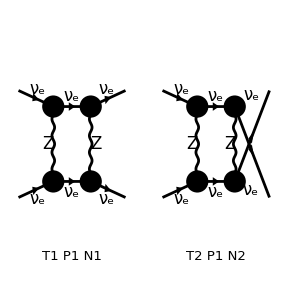

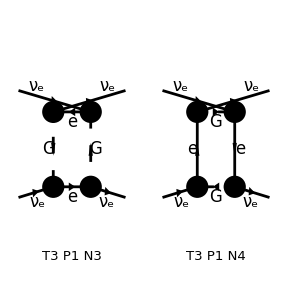

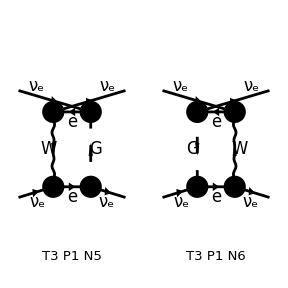

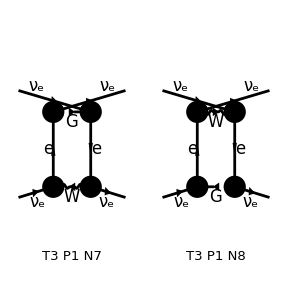

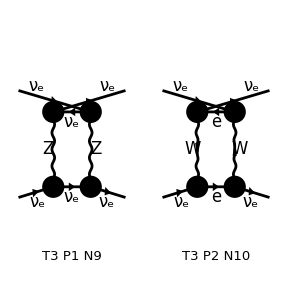

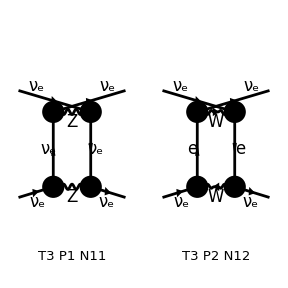

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 7 Particles insertions

> Top. 3: 7 Particles insertions

> Top. 4: 7 Particles insertions

> Top. 5: 7 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

in total: 28 Particles insertions

> Top. 1 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cfdg/fhegehgh.m, 0 diagrams

> Top. 3 aebf/cgde/ehfgfhgh.m, 0 diagrams

> Top. 4 aebf/cgdf/fhegehgh.m, 0 diagrams

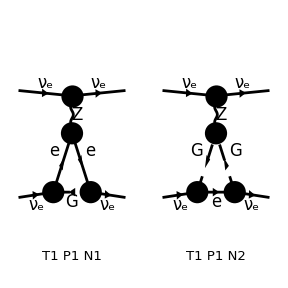

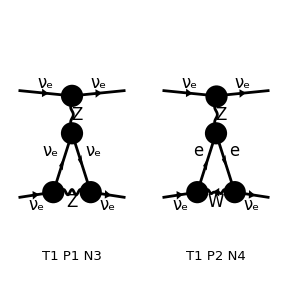

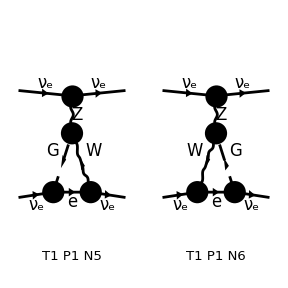

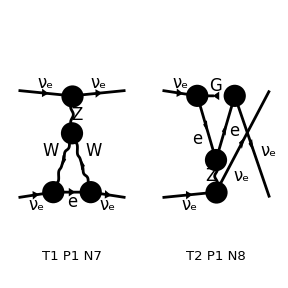

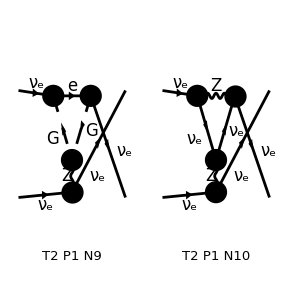

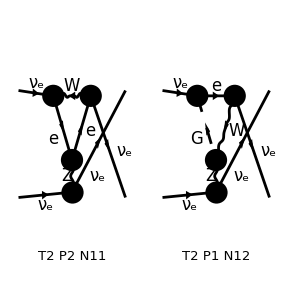

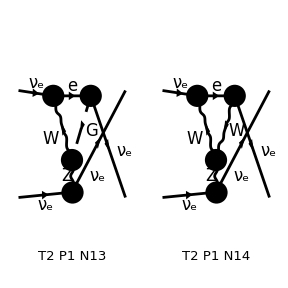

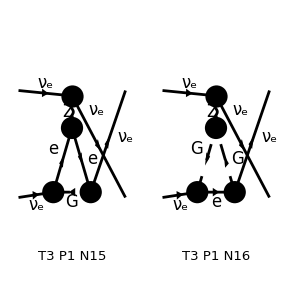

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 4 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 20 Particles insertions

> Top. 28: 3 Particles insertions

> Top. 29: 3 Particles insertions

> Top. 30: 20 Particles insertions

> Top. 31: 3 Particles insertions

> Top. 32: 3 Particles insertions

> Top. 33: 3 Particles insertions

> Top. 34: 3 Particles insertions

> Top. 35: 3 Particles insertions

> Top. 36: 3 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

in total: 72 Particles insertions

> Top. 1 aebf/cedf/egfggg.m, 0 diagrams

> Top. 2 aebf/cfde/egfggg.m, 0 diagrams

> Top. 3 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 4 aebf/cedg/effhghgh.m, 0 diagrams

> Top. 5 aebf/cedg/egghfhfh.m, 0 diagrams

> Top. 6 aebf/cfde/egfhghgh.m, 0 diagrams

> Top. 7 aebf/cfdg/efehghgh.m, 0 diagrams

> Top. 8 aebf/cfdg/fggheheh.m, 0 diagrams

> Top. 9 aebf/cgde/effhghgh.m, 0 diagrams

> Top. 10 aebf/cgde/egghfhfh.m, 0 diagrams

> Top. 11 aebf/cgdf/efehghgh.m, 0 diagrams

> Top. 12 aebf/cgdf/fggheheh.m, 0 diagrams

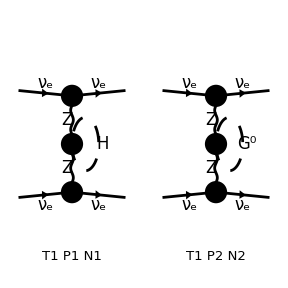

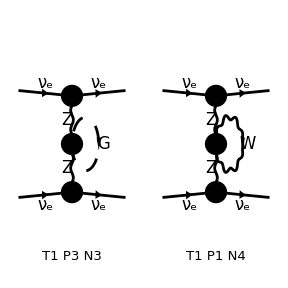

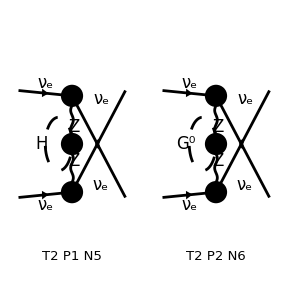

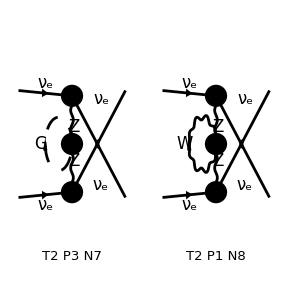

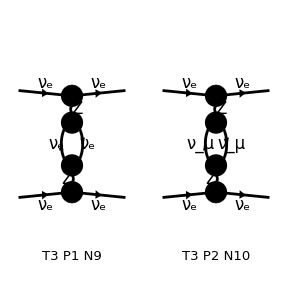

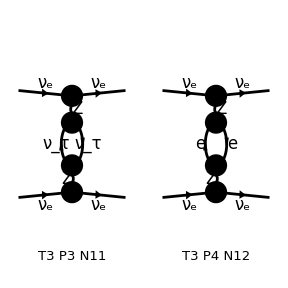

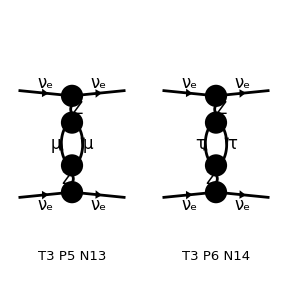

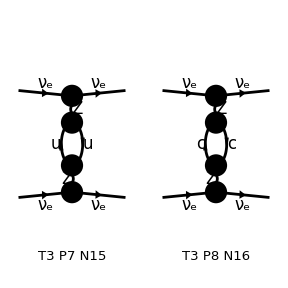

```mathematica
(**)
insertFieldsTree=InsertFields[topsLO,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsTree,ColumnsXRows->{2,1}];
(**)
insertFieldsBox=InsertFields[topsBox,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsBox,ColumnsXRows->{2,1}];
(**)
insertFieldsTri=InsertFields[topsTri,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsTri,ColumnsXRows->{2,1}];
(**)
insertFieldsSelf=InsertFields[topsSelf,{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFieldsSelf,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFieldsTree];
feynampBox=CreateFeynAmp[insertFieldsBox];
feynampTri=CreateFeynAmp[insertFieldsTri];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 10 Particles amplitudes

in total: 12 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 7 Particles amplitudes

> Top. 3: 7 Particles amplitudes

> Top. 4: 7 Particles amplitudes

in total: 28 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
AmplitudeBox=CalcFeynAmp[feynampBox,FermionChains->Chiral,Invariants->False,PaVeReduce->True]/.MZ2->mz2/.MW2->mw2;
AmplitudeTri=CalcFeynAmp[feynampTri,FermionChains->Chiral,Invariants->False,PaVeReduce->True]/.MZ2->mz2/.MW2->mw2;
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{F[1,{1}],k[2],0,{0,LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{F[1,{1}],k[4],0,{0,LeptonNumber}}}][8 Alfa gLnu^2 π (Den[-2 Pair[k[1],k[3]],mz2]+Den[-2 Pair[k[1],k[4]],mz2]) Mat[F1]]

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

```mathematica
squaredAmpBox=PolarizationSum[AmplitudeLO,AmplitudeBox,GaugeTerms->False];
prefacBox=Alfa*Alfa2*Conjugate[gLnu^2]*Pi*(s12+2* Conjugate[mz2])/(s13+ Conjugate[mz2])
ansBox=Collect[2^4*squaredAmpBox/prefacBox//.Abbr[]//.Subexpr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->0/.m4sq->0/.IGram[a_]:>1/a,{B0i[__],C0i[__],D0i[__],gLnu},Simplify]
```

```mathematica
squaredAmpTri=PolarizationSum[AmplitudeLO,AmplitudeTri,GaugeTerms->False];
prefacTri=Alfa*Alfa2*Conjugate[gLnu^2]*Pi*(s12+2* Conjugate[mz2])/(s13+ Conjugate[mz2]);
ansTri=Collect[2^4*squaredAmpTri/prefacTri//.Abbr[]//.Subexpr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->0/.m4sq->0/.IGram[a_]:>1/a,{A0[__],B0i[__],C0i[__],D0i[__],gLnu},Simplify]
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

(32 gLnu^4 s12^2 (-2 mz2+3 s13) B0i[bb0,-s13,0,0])/(s13 (mz2+s13) (-s12+s13-mz2^*))+(8 gLnu s12^2 (gRe ME2 (2 ME2-2 mw2-s13)+2 gLe mw2 (2 ME2-2 mw2+3 s13)) B0i[bb0,-s13,ME2,ME2])/(mw2 s13 (mz2+s13) sw2 (-s12+s13-mz2^*))+(4 gLnu s12^2 (cw2 ME2 (2 ME2-2 mw2-s13)+4 CW2 mw2 (2 ME2-2 mw2+s13)+ME2 (-2 ME2+2 mw2+s13) sw2) B0i[bb0,-s13,mw2,mw2])/(CW mw2 s13 (mz2+s13) SW sw2 (-s12+s13-mz2^*))+(8 gLnu s12^2 (4 CW2 mw2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s13))+cw2 ME2 (ME2^2+mw2^2-ME2 (2 mw2+s13))-ME2 (ME2^2-ME2 (2 mw2+s13)+mw2 (mw2+4 s13)) sw2) C0i[cc0,0,-s13,0,ME2,mw2,mw2])/(CW mw2 s13 (mz2+s13) SW sw2 (-s12+s13-mz2^*))-(64 gLnu^4 s12^2 (mz2-s13)^2 C0i[cc0,-s13,0,0,0,0,mz2])/(s13 (mz2+s13) (-s12+s13-mz2^*))-(16 gLnu s12^2 (gRe ME2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s13))+gLe (-4 ME2 mw2 (mw2-s13)+2 mw2 (mw2-s13)^2+ME2^2 (2 mw2-s13))) C0i[cc0,-s13,0,0,ME2,ME2,mw2])/(mw2 s13 (mz2+s13) sw2 (-s12+s13-mz2^*))-(64 Finite gLnu^4 s12^2 (2 mz2+s12))/((mz2+s12-s13) (mz2+s13) (s12-s13+mz2^*))-(4 Finite gLnu s12^2 (2 mz2+s12) (-cw2 ME2+2 CW (gRe ME2+4 gLe mw2) SW+ME2 sw2))/(CW mw2 (mz2+s12-s13) (mz2+s13) SW sw2 (s12-s13+mz2^*))-(64 gLnu^4 s12^2 (mz2^2 s12+2 s12 s13 (-s12+s13)+mz2 (s12^2-6 s12 s13+6 s13^2)) B0i[bb0,0,0,mz2])/((s12-s13) (mz2+s12-s13) s13 (mz2+s13) (s12-s13+mz2^*))+(8 gLnu s12^2 (cw2 ME2 (ME2-mw2) (mz2 s12+s12^2-2 s12 s13+2 s13^2)+4 CW2 mw2 (2 (2 mz2+s12) (s12-s13) s13+ME2 (mz2 s12+s12^2-2 s12 s13+2 s13^2)-mw2 (mz2 s12+s12^2-2 s12 s13+2 s13^2))+2 CW gRe ME2^2 mz2 s12 SW+4 CW gLe ME2 mw2 mz2 s12 SW-2 CW gRe ME2 mw2 mz2 s12 SW-4 CW gLe mw2^2 mz2 s12 SW+2 CW gRe ME2^2 s12^2 SW+4 CW gLe ME2 mw2 s12^2 SW-2 CW gRe ME2 mw2 s12^2 SW-4 CW gLe mw2^2 s12^2 SW-4 CW gRe ME2^2 s12 s13 SW-8 CW gLe ME2 mw2 s12 s13 SW+4 CW gRe ME2 mw2 s12 s13 SW+8 CW gLe mw2^2 s12 s13 SW+16 CW gLe mw2 mz2 s12 s13 SW+8 CW gLe mw2 s12^2 s13 SW+4 CW gRe ME2^2 s13^2 SW+8 CW gLe ME2 mw2 s13^2 SW-4 CW gRe ME2 mw2 s13^2 SW-8 CW gLe mw2^2 s13^2 SW-16 CW gLe mw2 mz2 s13^2 SW-8 CW gLe mw2 s12 s13^2 SW-ME2^2 mz2 s12 sw2+ME2 mw2 mz2 s12 sw2-ME2^2 s12^2 sw2+ME2 mw2 s12^2 sw2+2 ME2^2 s12 s13 sw2-2 ME2 mw2 s12 s13 sw2-2 ME2^2 s13^2 sw2+2 ME2 mw2 s13^2 sw2) B0i[bb0,0,ME2,mw2])/(CW mw2 (s12-s13) (mz2+s12-s13) s13 (mz2+s13) SW sw2 (s12-s13+mz2^*))+(32 gLnu^4 s12^2 (2 mz2-3 s12+3 s13) B0i[bb0,-s12+s13,0,0])/((s12-s13) (mz2+s12-s13) (s12-s13+mz2^*))+(8 gLnu s12^2 (gRe ME2 (-2 ME2+2 mw2+s12-s13)+2 gLe mw2 (-2 ME2+2 mw2-3 s12+3 s13)) B0i[bb0,-s12+s13,ME2,ME2])/(mw2 (s12-s13) (mz2+s12-s13) sw2 (s12-s13+mz2^*))+(4 gLnu s12^2 (cw2 ME2 (-2 ME2+2 mw2+s12-s13)+4 CW2 mw2 (-2 ME2+2 mw2-s12+s13)+ME2 (2 ME2-2 mw2-s12+s13) sw2) B0i[bb0,-s12+s13,mw2,mw2])/(CW mw2 (s12-s13) (mz2+s12-s13) SW sw2 (s12-s13+mz2^*))-(8 gLnu s12^2 (cw2 ME2 (ME2^2+mw2^2+ME2 (-2 mw2-s12+s13))+4 CW2 mw2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s12+2 s13))-ME2 (ME2^2+mw2 (mw2+4 s12-4 s13)+ME2 (-2 mw2-s12+s13)) sw2) C0i[cc0,0,-s12+s13,0,ME2,mw2,mw2])/(CW mw2 (s12-s13) (mz2+s12-s13) SW sw2 (s12-s13+mz2^*))+(64 gLnu^4 s12^2 (mz2-s12+s13)^2 C0i[cc0,-s12+s13,0,0,0,0,mz2])/((s12-s13) (mz2+s12-s13) (s12-s13+mz2^*))+(16 gLnu s12^2 (gLe (-4 ME2 mw2 (mw2-s12+s13)+2 mw2 (mw2-s12+s13)^2+ME2^2 (2 mw2-s12+s13))+gRe ME2 (ME2^2-2 ME2 mw2+mw2 (mw2-2 s12+2 s13))) C0i[cc0,-s12+s13,0,0,ME2,ME2,mw2])/(mw2 (s12-s13) (mz2+s12-s13) sw2 (s12-s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*(2*mz2 + s12)*(s12 + 2*conj(mz2))*pow(gLnu,2)*pow(Pi,2)*pow(s12,2)*pow(mz2 + s12 - s13,-1)*
   pow(mz2 + s13,-1)*pow(conj(gLnu),2)*pow(s12 - s13 + conj(mz2),-1)*pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.3) NLO Squared Amplitude calculation nu1 nu2 > nu1 nu2

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 7 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 7 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 1 Particles insertion

> Top. 14: 0 Particles insertions

> Top. 15: 5 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 4 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 0 Particles insertions

> Top. 35: 0 Particles insertions

> Top. 36: 0 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

> Top. 40: 0 Particles insertions

> Top. 41: 0 Particles insertions

> Top. 42: 0 Particles insertions

> Top. 43: 0 Particles insertions

> Top. 44: 0 Particles insertions

> Top. 45: 0 Particles insertions

> Top. 46: 0 Particles insertions

> Top. 47: 0 Particles insertions

> Top. 48: 0 Particles insertions

> Top. 49: 0 Particles insertions

> Top. 50: 0 Particles insertions

> Top. 51: 0 Particles insertions

> Top. 52: 0 Particles insertions

> Top. 53: 0 Particles insertions

> Top. 54: 0 Particles insertions

> Top. 55: 0 Particles insertions

> Top. 56: 0 Particles insertions

> Top. 57: 0 Particles insertions

> Top. 58: 0 Particles insertions

> Top. 59: 0 Particles insertions

> Top. 60: 0 Particles insertions

> Top. 61: 0 Particles insertions

> Top. 62: 0 Particles insertions

> Top. 63: 20 Particles insertions

> Top. 64: 3 Particles insertions

> Top. 65: 3 Particles insertions

> Top. 66: 0 Particles insertions

> Top. 67: 0 Particles insertions

> Top. 68: 0 Particles insertions

> Top. 69: 0 Particles insertions

> Top. 70: 0 Particles insertions

> Top. 71: 3 Particles insertions

> Top. 72: 3 Particles insertions

> Top. 73: 0 Particles insertions

> Top. 74: 0 Particles insertions

in total: 56 Particles insertions

> Top. 1 aebf/cedg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdf/fhegehgh.m, 0 diagrams

> Top. 3 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 4 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 5 aebf/cedf/egfggg.m, 0 diagrams

> Top. 6 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 7 aebf/cedg/effhghgh.m, 0 diagrams

> Top. 8 aebf/cedg/egghfhfh.m, 0 diagrams

> Top. 9 aebf/cgdf/efehghgh.m, 0 diagrams

> Top. 10 aebf/cgdf/fggheheh.m, 0 diagrams

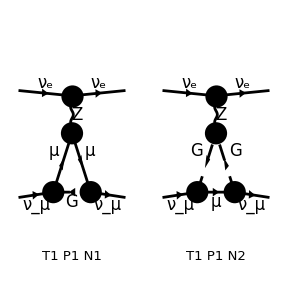

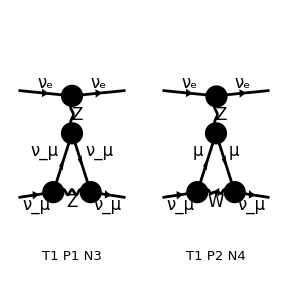

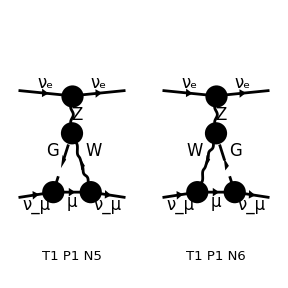

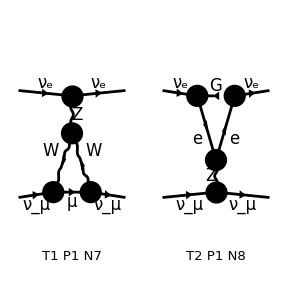

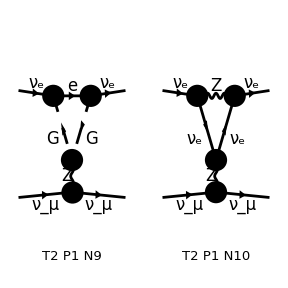

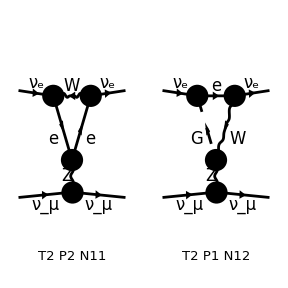

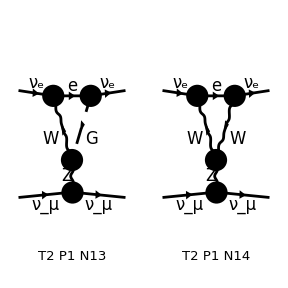

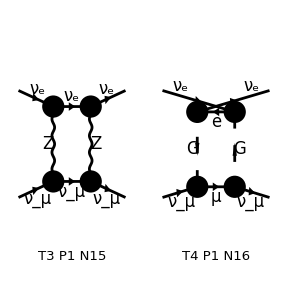

```mathematica
insertFields=InsertFields[topsV,{F[1,{1}],F[1,{2}]}->{F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{F[1,{2}],k[2],0,{0,LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{F[1,{2}],k[4],0,{0,LeptonNumber}}}][8 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 s12^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.4) LO Squared Amplitude calculation nu1 nu2bar > nu1 nu2bar

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{2}]}->{F[1,{1}],-F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

-Graphics-

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{2}],k[2],0,{0,-LeptonNumber}}}→{{F[1,{1}],k[3],0,{0,LeptonNumber}},{-F[1,{2}],k[4],0,{0,-LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

### 2.5) LO Squared Amplitude calculation nu1bar nu2 > nu1bar nu2

```mathematica
insertFields=InsertFields[topsLO,{-F[1,{1}],F[1,{2}]}->{-F[1,{1}],F[1,{2}]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5],!S}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

> Top. 1 aebf/cedf/ef.m, 0 diagrams

-Graphics-

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-amp-1.frm

running FORM...

ok

Amp[{{-F[1,{1}],k[1],0,{0,-LeptonNumber}},{F[1,{2}],k[2],0,{0,LeptonNumber}}}→{{-F[1,{1}],k[3],0,{0,-LeptonNumber}},{F[1,{2}],k[4],0,{0,LeptonNumber}}}][-4 Alfa gLnu^2 π Den[-2 Pair[k[1],k[3]],mz2] Mat[F1]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 1 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoPhotonInteraction/PartonicCalculation/fc-pol-1.frm

running FORM...

ok

```mathematica
ans=Simplify[2^4*squaredAmp//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->mfsq/.m4sq->mfsq/.MT2->mfsq]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 Alfa2 gLnu^2 π^2 (s12-s13)^2 (gLnu^*)^2)/((mz2+s13) (s13+mz2^*))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*Alfa2*pow(gLnu,2)*pow(Pi,2)*pow(s12 - s13,2)*pow(mz2 + s13,-1)*pow(conj(gLnu),2)*
   pow(s13 + conj(mz2),-1)

```mathematica
(* These results do not include the spin averaging factors of 1/2^n for each incoming fermion *)
```

## 3. diboson processes:

### 3.1) LO Squared Amplitude calculation nu nubar > WW

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{V[2],V[2]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

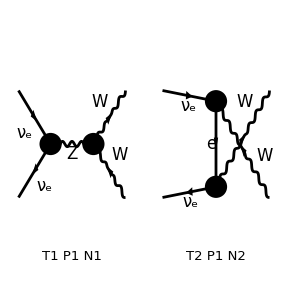

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{V[3],-V[3]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]/.MZ2->mz2
```

preparing FORM code in /Users/rhorry/Research/NeutrinoScattering/Notebooks/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{1}],k[2],0,{0,-LeptonNumber}}}→{{V[3],k[3],MW,-Charge},{-V[3],k[4],MW,Charge}}][-Alfa Pair2 π ((8 CW gLnu Den[2 Pair[k[1],k[2]],mz2])/SW+(2 Den[MW2-2 Pair[k[1],k[4]],0])/SW2) Mat[F1]-(2 Alfa π Den[MW2-2 Pair[k[1],k[4]],0] Mat[F2])/SW2+Alfa π ((8 CW gLnu Pair3 Den[2 Pair[k[1],k[2]],mz2])/SW+(4 Pair4 Den[MW2-2 Pair[k[1],k[4]],0])/SW2) Mat[F3]+Alfa Pair1 π ((8 CW gLnu Den[2 Pair[k[1],k[2]],mz2])/SW+(2 Den[MW2-2 Pair[k[1],k[4]],0])/SW2) Mat[F4]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 16 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoScattering/Notebooks/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoScattering/Notebooks/fc-pol-1.frm

running FORM...

ok

```mathematica
prefac=4 chiz Conjugate[chiz]Alfa2 Pi^2
```

4 Alfa2 chiz π^2 chiz^*

```mathematica
(* Drop some width effects when defining squared amplitude, since formally gammaw and gammaz -> 0 for on-shell W Z production*)
```

```mathematica
ans=Simplify[2^2*squaredAmp/prefac*chiz*(s12-mz2)*Conjugate[chiz]*(s12-Conjugate[mz2])//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->MW2/.m4sq->MW2]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf/.mz2->MZ2/.CW2->1-SW2/.gLnu->1/2/SW/CW//Simplify
```

1/(MW2^2 (MW2-s12+s13)^2 SW2^2)(-12 MW2^5 s12+MZ2^2 (s12-s13)^3 s13+MW2 MZ2 (s12-s13)^2 (MZ2 (3 s12-2 s13)+4 s13 (-s12+s13))+12 MW2^4 (MZ2 s12-s13 (s12+s13))+MW2^2 (s12-s13) (MZ2^2 (-6 s12+5 s13)+4 s13 (2 s12^2-4 s12 s13+3 s13^2)-4 MZ2 (3 s12^2-5 s12 s13+4 s13^2))+MW2^3 (-MZ2^2 s12+4 MZ2 (2 s12^2-3 s12 s13+3 s13^2)+4 (2 s12^3-4 s12^2 s13+7 s12 s13^2-6 s13^3)))

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

pow(MW2,-2)*(12*(MZ2*s12 - s13*(s12 + s13))*pow(MW2,4) - 12*s12*pow(MW2,5) + 
     MW2*MZ2*(MZ2*(3*s12 - 2*s13) + 4*s13*(-s12 + s13))*pow(s12 - s13,2) + 
     s13*pow(MZ2,2)*pow(s12 - s13,3) + 
     (s12 - s13)*pow(MW2,2)*((-6*s12 + 5*s13)*pow(MZ2,2) + 
        4*s13*(-4*s12*s13 + 2*pow(s12,2) + 3*pow(s13,2)) - 
        4*MZ2*(-5*s12*s13 + 3*pow(s12,2) + 4*pow(s13,2))) + 
     pow(MW2,3)*(-(s12*pow(MZ2,2)) + 4*MZ2*(-3*s12*s13 + 2*pow(s12,2) + 3*pow(s13,2)) + 
        4*(-4*s13*pow(s12,2) + 2*pow(s12,3) + 7*s12*pow(s13,2) - 6*pow(s13,3))))*
   pow(MW2 - s12 + s13,-2)*pow(SW2,-2)

### 3.2) LO Squared Amplitude calculation nu nubar > ZZ

```mathematica
insertFields=InsertFields[topsLO,{F[1,{1}],-F[1,{1}]}->{V[2],V[2]},InsertionLevel->{Particles},Model->"SMQCD",LastSelections->{!V[5]}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

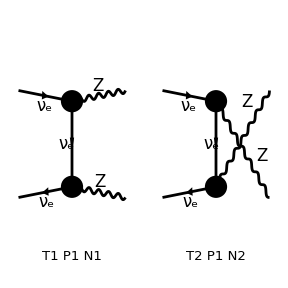

```mathematica
Paint[insertFields,ColumnsXRows->{2,1}];
```

```mathematica
feynampLO=CreateFeynAmp[insertFields];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

```mathematica
(* calculate the amplitude, but turn gauge terms off, and allowing for complex valued mz2 propagator *)
ClearProcess[];
AmplitudeLO=CalcFeynAmp[feynampLO,FermionChains->Chiral,Invariants->False]
```

preparing FORM code in /Users/rhorry/Research/NeutrinoScattering/Notebooks/fc-amp-1.frm

running FORM...

ok

Amp[{{F[1,{1}],k[1],0,{0,LeptonNumber}},{-F[1,{1}],k[2],0,{0,-LeptonNumber}}}→{{V[2],k[3],MZ,{}},{V[2],k[4],MZ,{}}}][-4 Alfa gLnu^2 π (Den[MZ2-2 Pair[k[1],k[3]],0]+Den[MZ2-2 Pair[k[1],k[4]],0]) Mat[F1]+Alfa gLnu^2 Pair2 π (4 Den[MZ2-2 Pair[k[1],k[3]],0]-4 Den[MZ2-2 Pair[k[1],k[4]],0]) Mat[F2]-Alfa gLnu^2 π (8 Pair3 Den[MZ2-2 Pair[k[1],k[3]],0]-8 Pair4 Den[MZ2-2 Pair[k[1],k[4]],0]) Mat[F3]-Alfa gLnu^2 Pair1 π (4 Den[MZ2-2 Pair[k[1],k[3]],0]-4 Den[MZ2-2 Pair[k[1],k[4]],0]) Mat[F4]]

```mathematica
squaredAmp=PolarizationSum[AmplitudeLO,GaugeTerms->False];
```

> 16 helicity matrix elements

preparing FORM code in /Users/rhorry/Research/NeutrinoScattering/Notebooks/fc-hel-1.frm

running FORM...

ok

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /Users/rhorry/Research/NeutrinoScattering/Notebooks/fc-pol-1.frm

running FORM...

ok

```mathematica
prefac=Alfa2 Pi^2
```

Alfa2 π^2

```mathematica
ans=Simplify[2^2*squaredAmp/prefac//.Abbr[]/.Den[a_,b_]:>1/(a - b )/.MomReplace/.Replacements2to2/.m3sq->MZ2/.m4sq->MZ2]/.s12-mz2->1/chiz/.gRu->gRf/.gLu->gLf
```

(64 gLnu^2 (2 MZ2^3 s12-MZ2 s12 (s12-2 s13)^2-2 MZ2^2 (s12^2-s12 s13+s13^2)+s13 (s12^3-3 s12^2 s13+4 s12 s13^2-2 s13^3)) (gLnu^*)^2)/((MZ2-s13)^2 (MZ2-s12+s13)^2)

```mathematica
CForm[ans]/.Conjugate->conj/.Power->pow
```

64*pow(gLnu,2)*pow(MZ2 - s13,-2)*(2*s12*pow(MZ2,3) - MZ2*s12*pow(s12 - 2*s13,2) - 
     2*pow(MZ2,2)*(-(s12*s13) + pow(s12,2) + pow(s13,2)) + 
     s13*(-3*s13*pow(s12,2) + pow(s12,3) + 4*s12*pow(s13,2) - 2*pow(s13,3)))*pow(MZ2 - s12 + s13,-2)*
   pow(conj(gLnu),2)

```mathematica
(* Try to integrate this thing? *)
```

```mathematica
(* dphi2 = 1 / ( 2 (4pi)^2 ) dphi dcostheta *)
```

```mathematica
test=(2 MZ2^3 s12-MZ2 s12 (s12-2 s13)^2-2 MZ2^2 (s12^2-s12 s13+s13^2)+s13 (s12^3-3 s12^2 s13+4 s12 s13^2-2 s13^3))/((MZ2-s13)^2 (MZ2-s12+s13)^2)
```

(2 MZ2^3 s12-2 MZ2^2 (s12^2-s12 s13+s13^2)-MZ2 s12 (s12-2 s13)^2+s13 (s12^3-3 s12^2 s13+4 s12 s13^2-2 s13^3))/((MZ2-s13)^2 (MZ2-s12+s13)^2)

```mathematica
(* s13 = E1 E3 ( 1 - β3 costheta *)
```

```mathematica
(* β3 = sqrt{1 - 4mz^2/shat }*)
```

```mathematica
Sqrt[1-4 mz2/s12]/.mz2->s12/y
```

√(1-4/y)

```mathematica
(* E3 = Sqrt[s12]/2 * (1 +)
```

```mathematica
(* y = s12 / mz2 *)
```

```mathematica
Expr=Simplify[test/.s13->s12/2 (1 -β  cth)/.MZ2->s12/y/.β->Sqrt[1-4/y],Assumptions->{0<y<1}]
```

-(2 y (cth^4 (y-4)^2 y+4 cth^2 (2 y^2-7 y-4)-(y-2)^2 (y+4)))/((-((cth^2-1) y^2)+4 (cth^2-1) y+4)^2)

```mathematica
integral=Integrate[Expr,{cth,-1,1},Assumptions->{y>4}]/.(y-2)/(√((y-4) y))->a
```

(8 ((y^2+4) coth^-1(a)-√((y-4) y^3)+2 √((y-4) y)))/((y-2) √((y-4) y))

```mathematica
(* Adding in the prefactors *)
```

```mathematica
FullSimplify[integral]
```

(8 (-√((y-4) y^3)+(y^2+4) coth^-1((y-2)/(√((y-4) y)))+2 √((y-4) y)))/((y-2) √((y-4) y))

```mathematica
ArcCoth
```

```mathematica
PSfactor=1/(2(4Pi^2))*2Pi
Fluxfactor=1/(2 s12)
Prefactor=64*Alfa2 Pi^2*gLnu^2*Conjugate[gLnu^2]
CForm[integral/.ArcCoth[x_]:>1/2*(Log[x+1]-Log[x-1])]/.ArcTan->atan/.Sqrt->sqrt/.Power->pow/.a->(y-2)/(√((y-4) y))
```

1/(4 π)

1/(2 s12)

64 π^2 Alfa2 gLnu^2 (Conjugate[gLnu])^2

8*pow(-2 + y,-1)*pow((-4 + y)*y,-1/2.)*
   (((-Log(-1 + (-2 + y)/Sqrt((-4 + y)*y)) + Log(1 + (-2 + y)/Sqrt((-4 + y)*y)))*(4 + pow(y,2)))/
      2. + 2*pow((-4 + y)*y,1/2.) - pow((-4 + y)*pow(y,3),1/2.))